```mathematica
tem1=Numerator[Total[rForm[onShellGraph[2][{{2,3,4},{5,6},{7,8},{9,1}},{0,0,0,0}]]]];
tem2=Numerator[Total[rForm[onShellGraph[2][{{3,4},{5,6},{7,8},{9,1,2}},{0,0,0,0}]]]];
tem3=Numerator[Total[rForm[onShellGraph[2][{{2,3},{4,5},{6,7,8},{9,1}},{0,0,0,0}]]]];
```

```mathematica
temp1=-{-R[2,1,3,4,6]R[Subscript[δ, 2],cap[{2,1},{3,4,6}],1,8,9],R[2,1,3,4,5]R[Subscript[δ, 2],cap[{2,1},{3,4,5}],1,8,9],R[2,3,4,5,6]R[Subscript[δ, 2],2,1,8,9],-R[2,1,4,5,6]R[Subscript[δ, 2],cap[{2,1},{4,5,6}],1,8,9],R[2,1,3,5,6]R[Subscript[δ, 2],cap[{2,1},{3,5,6}],1,8,9]}/.{3->4,4->5,5->6,6->7}/.Subscript[δ, 2]:>shift[{6,7},(ab[6,9,8,cap[{1,2},{4,5,7}]]+ab[7,9,8,cap[{1,2},{4,5,6}]]+ab[6,7,1,2] √(-(4 ab[1,2,4,5] ab[4,5,6,7] ab[6,7,8,9] ab[8,9,1,2])/(ab[1,2,6,7]^2 ab[4,5,8,9]^2)+(1-(ab[1,2,4,5] ab[6,7,8,9])/(ab[1,2,6,7] ab[4,5,8,9])-(ab[4,5,6,7] ab[8,9,1,2])/(ab[1,2,6,7] ab[4,5,8,9]))^2) ab[8,9,4,5])/(2 ab[7,8,9,cap[{1,2},{4,5,7}]])];
temp2={-R[2,3,4,5,7]R[Subscript[δ, 2],cap[{2,3},{4,5,7}],3,8,9],R[2,3,4,5,6]R[Subscript[δ, 2],cap[{2,3},{4,5,6}],3,8,9],R[2,4,5,6,7]R[Subscript[δ, 2],2,3,8,9],-R[2,3,5,6,7]R[Subscript[δ, 2],cap[{2,3},{5,6,7}],3,8,9],R[2,3,4,6,7]R[Subscript[δ, 2],cap[{2,3},{4,6,7}],3,8,9]}/.Subscript[δ, 2]:>shift[{6,7},(ab[6,9,8,cap[{2,3},{4,5,7}]]+ab[7,9,8,cap[{2,3},{4,5,6}]]+ab[6,7,2,3] √(-(4 ab[2,3,4,5] ab[4,5,6,7] ab[6,7,8,9] ab[8,9,2,3])/(ab[2,3,6,7]^2 ab[4,5,8,9]^2)+(1-(ab[2,3,4,5] ab[6,7,8,9])/(ab[2,3,6,7] ab[4,5,8,9])-(ab[4,5,6,7] ab[8,9,2,3])/(ab[2,3,6,7] ab[4,5,8,9]))^2) ab[8,9,4,5])/(2 ab[7,8,9,cap[{2,3},{4,5,7}]])];
temp3=-{-R[2,1,3,4,6]R[Subscript[δ, 2],cap[{2,1},{3,4,6}],1,8,9],R[2,1,3,4,5]R[Subscript[δ, 2],cap[{2,1},{3,4,5}],1,8,9],R[2,3,4,5,6]R[Subscript[δ, 2],2,1,8,9],-R[2,1,4,5,6]R[Subscript[δ, 2],cap[{2,1},{4,5,6}],1,8,9],R[2,1,3,5,6]R[Subscript[δ, 2],cap[{2,1},{3,5,6}],1,8,9]}/.Subscript[δ, 2]:>shift[{5,6},(ab[5,9,8,cap[{1,2},{3,4,6}]]+ab[6,9,8,cap[{1,2},{3,4,5}]]+ab[5,6,1,2] √(-(4 ab[1,2,3,4] ab[3,4,5,6] ab[5,6,8,9] ab[8,9,1,2])/(ab[1,2,5,6]^2 ab[3,4,8,9]^2)+(1-(ab[1,2,3,4] ab[5,6,8,9])/(ab[1,2,5,6] ab[3,4,8,9])-(ab[3,4,5,6] ab[8,9,1,2])/(ab[1,2,5,6] ab[3,4,8,9]))^2) ab[8,9,3,4])/(2 ab[6,8,9,cap[{1,2},{3,4,6}]])];
```

```mathematica
{((tem1-Total[temp1])//todmatrix)/.DmatrixEval[{6,4},{7,4},{6,4},{6,4}]//neab//Simplify,
((tem2-Total[temp2])//todmatrix)/.DmatrixEval[{6,4},{7,4},{6,4},{6,4}]//neab//Simplify,
((tem3-Total[temp3])//todmatrix)/.DmatrixEval[{2,8},{1,8},{3,8},{4,8}]//neab//Simplify}
```

{0,0,0}

```mathematica
randomPositiveZs[20]
neabp[exp_]:=exp/.shifexp//.capexpand/.ab[x__]:>Det[Zs⟦{x}⟧];
abfactor[exp_]:=Module[{lis=Union@@Cases[exp//.shifexp//.capexpand,_ab,Infinity]/.ab->List},If[Position[exp/(ab@@@Subsets[lis,{4}])//neab,_Integer]=!={},ab@@@Subsets[lis,{4}][[Flatten[Position[exp/(ab@@@Subsets[lis,{4}])//neab,_Integer]]]],exp]];
taure={τ:>2(a-2c+a t)/(t^2-1)};
acre={a:>(ab[1,2,3,8]ab[1,2,7,cap[{6,8},{4,5,7}]])/(ab[2,3,7,8]ab[1,6,7,cap[{8,2},{1,4,5}]]),c:>(ab[1,2,3,8]ab[1,2,4,5]ab[1,2,7,8]ab[1,6,7,8]ab[4,5,6,7])/(ab[2,3,7,8] ab[1,6,7,cap[{8,2},{1,4,5}]]^2)};
jacp1=-Simplify[(1/2+1/2(-4 c+a (1+t)^2)/(-4 c t+a (1+t)^2))D[τ/.taure,t]];
jacm1=Simplify[(1/2-1/2(-4 c+a (1+t)^2)/(-4 c t+a (1+t)^2))D[τ/.taure,t]];
shiftp1=shift[{6,7},ab[1,6,7,cap[{8,2},{1,4,5}]]/(ab[1,2,7,8] ab[1,4,5,7]) ((c (1-t))/(a-2 c+a t))+ab[1,4,5,6]/ab[7,1,4,5]];
shiftm1=shift[{6,7},ab[6,1,4,5]/ab[1,4,5,7]+ab[1,6,7,cap[{8,2},{1,4,5}]]/(2ab[1,2,7,8]ab[1,4,5,7])(-1-t)];
```

```mathematica
((ab[1,2,3,8]ab[1,2,4,5]ab[1,2,7,8]ab[1,6,7,8]ab[4,5,6,7])/(ab[2,3,7,8] ab[1,6,7,cap[{8,2},{1,4,5}]]^2))/((ab[1,2,3,8]ab[1,2,7,cap[{6,8},{4,5,7}]])/(ab[2,3,7,8]ab[1,6,7,cap[{8,2},{1,4,5}]]))
```

```mathematica
((2ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7])/(ab[1,2,7,cap[{6,8},{4,5,7}]] ab[1,6,7,cap[{8,2},{1,4,5}]])-1)(2(ab[1,2,3,8]ab[1,2,7,cap[{6,8},{4,5,7}]])/(ab[2,3,7,8]ab[1,6,7,cap[{8,2},{1,4,5}]]))//Factor
```

-(2 ab[1,2,3,8] (ab[1,2,7,cap[{6,8},{4,5,7}]] ab[1,6,7,cap[{8,2},{1,4,5}]]-2 ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7]))/(ab[1,6,7,cap[{8,2},{1,4,5}]]^2 ab[2,3,7,8])

{ab[1,2,3,8]}

```mathematica
temp11={#/.Sqrt[x_]:>sqrt[Limit[x//fullabB,e->0]]/.sortR/.Rtodab/.dabBexp/.dabshifexp/.{dab[1,x___,cap[{2,1},a___],y___,2]:>0}}&/@temp1;
temp12={#/.Sqrt[x_]:>-sqrt[Limit[x//fullabB,e->0]]/.sortR/.Rtodab/.dabBexp/.dabshifexp/.{dab[1,x___,cap[{2,1},a___],y___,2]:>0}}&/@temp1;
```

```mathematica
tauinf1=1/(τ-Subscript[X, 1]){(ab[1,2,3,8]dab[1,6,cap[{2,1},{4,5,7}],8,7] R[1,2,4,5,7])/(ab[2,3,7,8]ab[6,7,8,1]ab[1,2,7,8]ab[1,4,5,7]),-(ab[1,2,3,8]dab[1,6,cap[{2,1},{4,5,6}],8,7] R[1,2,4,5,6])/(ab[2,3,7,8]ab[6,7,8,1]ab[1,2,7,8]ab[1,4,5,6]),(ab[1,2,3,8] dab[1,6,2,8,7] R[2,4,5,6,7])/(ab[2,3,7,8]ab[6,7,8,1]ab[1,2,7,8]),(ab[1,2,3,8]dab[1,6,cap[{2,1},{5,6,7}],8,7] R[1,2,5,6,7])/(ab[2,3,7,8]ab[6,7,8,1]ab[1,2,7,8]ab[1,5,6,7]),(-ab[1,2,3,8]dab[1,6,cap[{2,1},{4,6,7}],8,7] R[1,2,4,6,7])/(ab[2,3,7,8]ab[6,7,8,1]ab[1,2,7,8]ab[1,4,6,7])};
tauzer1={(ab[1,2,3,8] dab[1,6,2,8,7] R[1,2,4,5,7])/(τ ab[1,2,7,8] ab[1,6,7,8] ab[2,3,7,8]),0,0,0,0};
```

```mathematica
ttauinf1=(ab[1,2,3,8] dab[1,6,2,8,7]R[1,4,5,6,7])/(ab[1,2,7,8] ab[2,3,7,8] ab[6,7,8,1]) 1/(τ+(2 ab[1,2,3,8] ab[1,2,7,cap[{6,8},{4,5,7}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[2,3,7,8])-(4 ab[1,2,3,8] ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7])/(ab[1,6,7,cap[{8,2},{1,4,5}]]^2 ab[2,3,7,8]));
```

```mathematica
tauinf3=1/(τ-Subscript[X, 3])(ab[1,2,3,8]  dab[1,cap[{5,6},{3,4,1}],2,8,7])/(ab[1,2,7,8]ab[7,8,1,cap[{5,6},{3,4,1}]] ab[2,3,7,8]){-R[1,2,3,4,6],R[1,2,3,4,5],-R[2,3,4,5,6],-R[1,2,4,5,6],R[1,2,3,5,6]};
```

```mathematica
ttauinf3=1/(τ-Subscript[X, 3])(-ab[1,2,3,8]  dab[1,cap[{5,6},{3,4,1}],2,8,7])/(ab[1,2,7,8]ab[7,8,1,cap[{5,6},{3,4,1}]] ab[2,3,7,8])R[1,3,4,5,6];
```

```mathematica
tauzer4={(ab[1,2,3,8] dab[6,cap[{2,3},{4,5,7}],1,8,7] R[2,3,4,5,7])/(τ ab[2,3,7,8]ab[7,8,1,cap[{2,3},{4,5,7}]]ab[7,8,1,6]),0,0,0,0};
```

```mathematica
hard1p={(ab[1,2,3,8] dlog[(-1+t+(2 ab[1,2,6,7] ab[1,4,5,7] ab[6,7,8,cap[{5,4},{1,2,8}]])/(ab[1,2,7,cap[{6,8},{4,5,7}]] ab[1,6,7,cap[{8,2},{1,4,5}]]))/(-1+t)] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,2,4,5,7])/ab[2,3,7,8],-(ab[1,2,3,8] dlog[(-1+t+(2 ab[1,2,6,7] ab[1,4,5,6] ab[8,1,2,cap[{5,4},{6,7,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,6,cap[{1,2},{6,7,8}]]))/(-1+t)] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,2,4,5,6])/ab[2,3,7,8],(ab[1,2,3,8] dlog[(-1+t+(2 ab[1,2,6,7] ab[6,7,8,cap[{5,4},{1,2,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[2,6,7,8]))/(-1+t)] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[2,4,5,6,7])/ab[2,3,7,8],(ab[1,2,3,8] dlog[(-1+t+(2 ab[1,5,6,7] ab[8,1,2,cap[{4,5},{6,7,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[5,6,7,8]))/(-1+t)] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,2,5,6,7])/ab[2,3,7,8],-(ab[1,2,3,8] dlog[(-1+t+(2 ab[1,4,6,7] ab[6,7,8,cap[{5,4},{1,2,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,6,7,8]))/(-1+t)] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,2,4,6,7])/ab[2,3,7,8]};
```

```mathematica
hard1m={(ab[1,2,3,8] dlog[1+t] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,2,4,5,7])/ab[2,3,7,8],-(ab[1,2,3,8] dlog[(1+t)/(1+t+(2 ab[1,2,7,8] ab[1,4,5,6])/ab[1,6,7,cap[{8,2},{1,4,5}]])] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,2,4,5,6])/ab[2,3,7,8],(ab[1,2,3,8] dlog[(1+t)/(1+t+(2 ab[1,2,4,5] ab[1,2,7,8] ab[4,5,6,7])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[2,4,5,7]))] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[2,4,5,6,7])/ab[2,3,7,8],(ab[1,2,3,8] dlog[(1+t)/(1+t-(2 ab[1,2,4,5] ab[1,2,7,8] ab[1,5,6,7])/(ab[1,2,5,7] ab[1,6,7,cap[{8,2},{1,4,5}]]))] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,2,5,6,7])/ab[2,3,7,8],-(ab[1,2,3,8] dlog[(1+t)/(1+t-(2 ab[1,2,4,5] ab[1,2,7,8] ab[1,4,6,7])/(ab[1,2,4,7] ab[1,6,7,cap[{8,2},{1,4,5}]]))] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,2,4,6,7])/ab[2,3,7,8]};
```

```mathematica
temp121={(ab[1,2,3,8] dab[1,6,2,8,7] R[1,2,4,5,7])/((1+t) ab[1,2,7,8] ab[1,6,7,8] ab[2,3,7,8]),(-2 ab[1,2,3,8] dab[1,6,cap[{2,1},{4,5,6}],8,7] R[1,2,4,5,6])/((1+t) ab[1,6,7,8] ab[8,1,2,cap[{6,7},{1,4,5}]] ab[2,3,7,8](t+(ab[1,2,7,8] ab[1,4,5,6]+ab[1,2,6,8] ab[1,4,5,7])/(-ab[1,2,7,8] ab[1,4,5,6]+ab[1,2,6,8] ab[1,4,5,7]))),(2 ab[1,2,3,8] ab[1,2,4,5] ab[4,5,6,7] dab[1,6,2,8,7] R[2,4,5,6,7])/((1+t) ab[1,6,7,8] ab[1,6,7,cap[{8,2},{1,4,5}]] ab[2,3,7,8] ab[2,4,5,7] (1+t+(2 ab[1,2,4,5] ab[1,2,7,8] ab[4,5,6,7])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[2,4,5,7]))),(-2 ab[1,2,3,8] ab[1,2,4,5] dab[1,6,cap[{2,1},{5,6,7}],8,7] R[1,2,5,6,7])/((1+t) ab[1,2,5,7] ab[1,6,7,8] (1+t-(2 ab[1,2,4,5] ab[1,2,7,8] ab[1,5,6,7])/(ab[1,2,5,7] ab[1,6,7,cap[{8,2},{1,4,5}]])) ab[1,6,7,cap[{8,2},{1,4,5}]] ab[2,3,7,8]),(2 ab[1,2,3,8] ab[1,2,4,5] dab[1,6,cap[{2,1},{4,6,7}],8,7] R[1,2,4,6,7])/((1+t) ab[1,2,4,7] ab[1,6,7,8] (1+t-(2 ab[1,2,4,5] ab[1,2,7,8] ab[1,4,6,7])/(ab[1,2,4,7] ab[1,6,7,cap[{8,2},{1,4,5}]])) ab[1,6,7,cap[{8,2},{1,4,5}]] ab[2,3,7,8])};
```

```mathematica
temp111={(2 ab[1,2,3,8] (-1+(ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7])/(ab[1,2,7,cap[{6,8},{4,5,7}]] ab[1,6,7,cap[{8,2},{1,4,5}]])) dab[1,6,cap[{2,1},{4,5,7}],8,7] R[1,2,4,5,7])/((-1+t) ab[1,2,7,8] ab[1,4,5,7] ab[1,6,7,8] ab[2,3,7,8] (1+t-(2 ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7])/(ab[1,2,7,cap[{6,8},{4,5,7}]] ab[1,6,7,cap[{8,2},{1,4,5}]]))),(2 ab[1,2,3,8] ab[1,2,6,7] ab[8,1,2,cap[{5,4},{6,7,8}]]dab[1,6,cap[{2,1},{4,5,6}],8,7] R[1,2,4,5,6])/((-1+t) ab[1,2,7,8] ab[1,6,7,8] ab[1,6,7,cap[{8,2},{1,4,5}]] ab[2,3,7,8] ab[4,5,6,cap[{1,2},{6,7,8}]](t-1+(2 ab[1,2,6,7] ab[1,4,5,6] ab[8,1,2,cap[{5,4},{6,7,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,6,cap[{1,2},{6,7,8}]]))),(2 ab[1,2,3,8] ab[1,2,6,7]  ab[8,1,2,cap[{5,4},{6,7,8}]]dab[1,6,2,8,7] R[2,4,5,6,7])/((-1+t) ab[1,2,7,8] ab[1,6,7,8] ab[1,6,7,cap[{8,2},{1,4,5}]] ab[2,3,7,8] ab[2,6,7,8] (-1+t+(2 ab[1,2,6,7] ab[6,7,8,cap[{5,4},{1,2,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[2,6,7,8]))),(2 ab[1,2,3,8] ab[8,1,2,cap[{5,4},{6,7,8}]] dab[1,6,cap[{2,1},{5,6,7}],8,7] R[1,2,5,6,7])/((-1+t) ab[1,2,7,8] ab[1,6,7,8] ab[1,6,7,cap[{8,2},{1,4,5}]] ab[2,3,7,8] ab[5,6,7,8] (-1+t-(2 ab[1,5,6,7] ab[8,1,2,cap[{5,4},{6,7,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[5,6,7,8]))),(-2 ab[1,2,3,8] ab[1,2,6,7] ab[8,1,2,cap[{5,4},{6,7,8}]]dab[1,6,cap[{2,1},{4,6,7}],8,7] R[1,2,4,6,7])/((-1+t)  ab[1,2,7,8] ab[1,6,7,8] ab[1,6,7,cap[{8,2},{1,4,5}]] ab[2,3,7,8] ab[6,7,8,cap[{1,2},{4,6,7}]](-1+t+(2 ab[1,2,6,7] ab[1,4,6,7] ab[6,7,8,cap[{5,4},{1,2,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[6,7,8,cap[{1,2},{4,6,7}]])))};
```

```mathematica
(* R invariant check  *)
```

```mathematica
Table[Simplify[(Limit[jacp1 Total[temp11[[i]]/.shift[{6,7},x___]:>shiftp1]//fullabB,e->0]/.taure/.acre/.dabcapexpand//Simplify//neabp//Simplify)-(temp111[[i]]/.dabcapexpand//neabp)],{i,5}]
```

Part::partd: 部分指定 temp11⟦1⟧ 比对象深度更长.

Part::partd: 部分指定 temp11⟦2⟧ 比对象深度更长.

Part::partd: 部分指定 temp11⟦3⟧ 比对象深度更长.

General::stop: 在本次计算中，Part::partd 的进一步输出将被抑制.

{(5260800 (8304102025265+10013036594957 t) (1+temp11))/(236320476320932795979 (-1+t)^2 (1+t))+(657836734144948207616 dab[1,6,2,8,7] R[1,2,4,5,7])/(2409457189222125 (-1+t) (8304102025265+10013036594957 t)),(5260800 (8304102025265+10013036594957 t) (2+temp11))/(236320476320932795979 (-1+t)^2 (1+t))-(19494817069767589888 dab[1,6,2,8,7] R[1,2,4,5,6])/(89239155156375 (-1+t) (4844137308911+9812098347931 t)),(5260800 (8304102025265+10013036594957 t) (3+temp11))/(236320476320932795979 (-1+t)^2 (1+t))+(226683919415902208 dab[1,6,2,8,7] R[2,4,5,6,7])/(267717465469125 (-1+t) (-27737507719+84544622668 t)),(5260800 (8304102025265+10013036594957 t) (4+temp11))/(236320476320932795979 (-1+t)^2 (1+t))+(88737210260258816 dab[1,6,2,8,7] R[1,2,5,6,7])/(803152396407375 (-1+t) (6833458483+579072758 t)),(5260800 (8304102025265+10013036594957 t) (5+temp11))/(236320476320932795979 (-1+t)^2 (1+t))-(49484691822608384 dab[1,6,2,8,7] R[1,2,4,6,7])/(2409457189222125 (-1+t) (1088340399+289536379 t))}

```mathematica
Table[Simplify[(Limit[jacm1 Total[temp12[[i]]/.shift[{6,7},x___]:>shift[{6,7},ab[6,1,4,5]/ab[1,4,5,7]+ab[1,6,7,cap[{8,2},{1,4,5}]]/(2ab[1,2,7,8]ab[1,4,5,7])(-1-t)]]//fullabB,e->0]/.taure/.acre/.dabcapexpand//Simplify//neabp//Simplify)-(temp121[[i]]/.dabcapexpand//neabp)],{i,5}]
```

{0,0,0,0,0}

```mathematica
temp121
```

{(ab[1,2,3,8] dab[1,6,2,8,7] R[1,2,4,5,7])/((1+t) ab[1,2,7,8] ab[1,6,7,8] ab[2,3,7,8]),-(2 ab[1,2,3,8] dab[1,6,cap[{2,1},{4,5,6}],8,7] R[1,2,4,5,6])/((1+t) (t+(ab[1,2,7,8] ab[1,4,5,6]+ab[1,2,6,8] ab[1,4,5,7])/(-ab[1,2,7,8] ab[1,4,5,6]+ab[1,2,6,8] ab[1,4,5,7])) ab[1,6,7,8] ab[2,3,7,8] ab[8,1,2,cap[{6,7},{1,4,5}]]),(2 ab[1,2,3,8] ab[1,2,4,5] ab[4,5,6,7] dab[1,6,2,8,7] R[2,4,5,6,7])/((1+t) ab[1,6,7,8] ab[1,6,7,cap[{8,2},{1,4,5}]] ab[2,3,7,8] ab[2,4,5,7] (1+t+(2 ab[1,2,4,5] ab[1,2,7,8] ab[4,5,6,7])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[2,4,5,7]))),-(2 ab[1,2,3,8] ab[1,2,4,5] dab[1,6,cap[{2,1},{5,6,7}],8,7] R[1,2,5,6,7])/((1+t) ab[1,2,5,7] ab[1,6,7,8] (1+t-(2 ab[1,2,4,5] ab[1,2,7,8] ab[1,5,6,7])/(ab[1,2,5,7] ab[1,6,7,cap[{8,2},{1,4,5}]])) ab[1,6,7,cap[{8,2},{1,4,5}]] ab[2,3,7,8]),(2 ab[1,2,3,8] ab[1,2,4,5] dab[1,6,cap[{2,1},{4,6,7}],8,7] R[1,2,4,6,7])/((1+t) ab[1,2,4,7] ab[1,6,7,8] (1+t-(2 ab[1,2,4,5] ab[1,2,7,8] ab[1,4,6,7])/(ab[1,2,4,7] ab[1,6,7,cap[{8,2},{1,4,5}]])) ab[1,6,7,cap[{8,2},{1,4,5}]] ab[2,3,7,8])}

```mathematica
Table[((hard1m[[i]]/.dlog[x_]:>D[Log[x],t]/.sortab/.qlogtodab)-(temp121[[i]])/.sortdab/.dabcapexpand//neabp)/.sortdab//Simplify,{i,5}]
```

{0,0,0,0,0}

```mathematica
(hard1m[[i]]/.dlog[x_]:>D[Log[x],t]/.sortab/.qlogtodab)
```

```mathematica
Collect[Total[(ab[1,2,3,8]/ab[2,3,7,8])^-1 hard1m]/.dlog[x_/y_]:>dlog[x]-dlog[y],dlog[_]]//Simplify
```

```mathematica
Qlog[ab[7,8,1,2]/ab[7,8,1,6]] (dlog[1+t+(2 ab[1,2,7,8] ab[1,4,5,6])/ab[1,6,7,cap[{8,2},{1,4,5}]]] R[1,2,4,5,6]+dlog[1+t-(2 ab[1,2,4,5] ab[1,2,7,8] ab[1,4,6,7])/(ab[1,2,4,7] ab[1,6,7,cap[{8,2},{1,4,5}]])] R[1,2,4,6,7]-dlog[1+t-(2 ab[1,2,4,5] ab[1,2,7,8] ab[1,5,6,7])/(ab[1,2,5,7] ab[1,6,7,cap[{8,2},{1,4,5}]])] R[1,2,5,6,7]-dlog[1+t+(2 ab[1,2,4,5] ab[1,2,7,8] ab[4,5,6,7])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[2,4,5,7])] R[2,4,5,6,7]+dlog[1+t] R[1,4,5,6,7])
```

Qlog[ab[7,8,1,2]/ab[7,8,1,6]] (dlog[1+t+(2 ab[1,2,7,8] ab[1,4,5,6])/ab[1,6,7,cap[{8,2},{1,4,5}]]] R[1,2,4,5,6]+dlog[1+t-(2 ab[1,2,4,5] ab[1,2,7,8] ab[1,4,6,7])/(ab[1,2,4,7] ab[1,6,7,cap[{8,2},{1,4,5}]])] R[1,2,4,6,7]-dlog[1+t-(2 ab[1,2,4,5] ab[1,2,7,8] ab[1,5,6,7])/(ab[1,2,5,7] ab[1,6,7,cap[{8,2},{1,4,5}]])] R[1,2,5,6,7]+dlog[1+t] R[1,4,5,6,7]-dlog[1+t+(2 ab[1,2,4,5] ab[1,2,7,8] ab[4,5,6,7])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[2,4,5,7])] R[2,4,5,6,7])

```mathematica
sixR[1,4,5,6,7,2]/.sortR
```

```mathematica
-R[1,2,4,5,6]+R[1,2,4,5,7]-R[1,2,4,6,7]+R[1,2,5,6,7]+R[2,4,5,6,7]-(-R[1,2,4,5,6]+R[1,2,4,5,7]-R[1,2,4,6,7]+R[1,2,5,6,7]+R[2,4,5,6,7])
```

0

```mathematica
hard1p
```

```mathematica
Collect[Total[(ab[1,2,3,8]/ab[2,3,7,8])^-1 hard1p]/.dlog[x_/y_]:>dlog[x]-dlog[y],dlog[_]]//Simplify
```

```mathematica
Qlog[ab[7,8,1,2]/ab[7,8,1,6]] (-dlog[-1+t+(2 ab[1,2,6,7] ab[1,4,5,6] ab[8,1,2,cap[{5,4},{6,7,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,6,cap[{1,2},{6,7,8}]])] R[1,2,4,5,6]+dlog[-1+t+(2 ab[1,2,6,7] ab[1,4,5,7] ab[6,7,8,cap[{5,4},{1,2,8}]])/(ab[1,2,7,cap[{6,8},{4,5,7}]] ab[1,6,7,cap[{8,2},{1,4,5}]])] R[1,2,4,5,7]-dlog[-1+t+(2 ab[1,4,6,7] ab[6,7,8,cap[{5,4},{1,2,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,6,7,8])] R[1,2,4,6,7]+dlog[-1+t+(2 ab[1,5,6,7] ab[8,1,2,cap[{4,5},{6,7,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[5,6,7,8])] R[1,2,5,6,7]+dlog[-1+t] (-R[1,4,5,6,7])+dlog[-1+t+(2 ab[1,2,6,7] ab[6,7,8,cap[{5,4},{1,2,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[2,6,7,8])] R[2,4,5,6,7])
```

Qlog[ab[7,8,1,2]/ab[7,8,1,6]] (-dlog[-1+t+(2 ab[1,2,6,7] ab[1,4,5,6] ab[8,1,2,cap[{5,4},{6,7,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,6,cap[{1,2},{6,7,8}]])] R[1,2,4,5,6]+dlog[-1+t+(2 ab[1,2,6,7] ab[1,4,5,7] ab[6,7,8,cap[{5,4},{1,2,8}]])/(ab[1,2,7,cap[{6,8},{4,5,7}]] ab[1,6,7,cap[{8,2},{1,4,5}]])] R[1,2,4,5,7]-dlog[-1+t+(2 ab[1,4,6,7] ab[6,7,8,cap[{5,4},{1,2,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,6,7,8])] R[1,2,4,6,7]+dlog[-1+t+(2 ab[1,5,6,7] ab[8,1,2,cap[{4,5},{6,7,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[5,6,7,8])] R[1,2,5,6,7]-dlog[-1+t] R[1,4,5,6,7]+dlog[-1+t+(2 ab[1,2,6,7] ab[6,7,8,cap[{5,4},{1,2,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[2,6,7,8])] R[2,4,5,6,7])

```mathematica
sixR[1,4,5,6,7,2]/.sortR
```

-R[1,2,4,5,6]+R[1,2,4,5,7]-R[1,2,4,6,7]+R[1,2,5,6,7]+R[2,4,5,6,7]

```mathematica
boxfun1=Li[1]-Li[((t-1)(ab[1,2,4,5]ab[1,6,7,8]ab[4,5,6,7]ab[1,2,7,8])/(ab[1,2,6,7]ab[1,4,5,7]ab[6,7,8,cap[{1,2},{4,5,8}]])+t+1)/((ab[4,5,7,8]ab[1,6,7,cap[{8,2},{1,4,5}]])/(ab[1,4,5,7]ab[6,7,8,cap[{1,2},{4,5,8}]])(t-1)+2)]-Li[((1+t)(1-(ab[1,2,4,5]ab[1,6,7,8])/(ab[1,2,6,7]ab[1,4,5,8])))/((1+t)-(t-1)(ab[1,2,4,5]ab[1,6,7,8])/(ab[1,2,6,7]ab[1,4,5,8]))]+log[((t-1)(ab[1,2,4,5]ab[1,6,7,8]ab[4,5,6,7]ab[1,2,7,8])/(ab[1,2,6,7]ab[1,4,5,7]ab[6,7,8,cap[{1,2},{4,5,8}]])+t+1)/((ab[4,5,7,8]ab[1,6,7,cap[{8,2},{1,4,5}]])/(ab[1,4,5,7]ab[6,7,8,cap[{1,2},{4,5,8}]])(t-1)+2)]log[((1+t)(1-(ab[1,2,4,5]ab[1,6,7,8])/(ab[1,2,6,7]ab[1,4,5,8])))/((1+t)-(t-1)(ab[1,2,4,5]ab[1,6,7,8])/(ab[1,2,6,7]ab[1,4,5,8]))]-1/2 log[(1-((t-1)(ab[1,2,4,5]ab[1,6,7,8]ab[4,5,6,7]ab[1,2,7,8])/(ab[1,2,6,7]ab[1,4,5,7]ab[6,7,8,cap[{1,2},{4,5,8}]])+t+1)/((ab[4,5,7,8]ab[1,6,7,cap[{8,2},{1,4,5}]])/(ab[1,4,5,7]ab[6,7,8,cap[{1,2},{4,5,8}]])(t-1)+2))((1+t)(1-(ab[1,2,4,5]ab[1,6,7,8])/(ab[1,2,6,7]ab[1,4,5,8])))/((1+t)-(t-1)(ab[1,2,4,5]ab[1,6,7,8])/(ab[1,2,6,7]ab[1,4,5,8]))]log[((t-1)(ab[1,2,4,5]ab[1,6,7,8]ab[4,5,6,7]ab[1,2,7,8])/(ab[1,2,6,7]ab[1,4,5,7]ab[6,7,8,cap[{1,2},{4,5,8}]])+t+1)/((ab[4,5,7,8]ab[1,6,7,cap[{8,2},{1,4,5}]])/(ab[1,4,5,7]ab[6,7,8,cap[{1,2},{4,5,8}]])(t-1)+2)(1-((1+t)(1-(ab[1,2,4,5]ab[1,6,7,8])/(ab[1,2,6,7]ab[1,4,5,8])))/((1+t)-(t-1)(ab[1,2,4,5]ab[1,6,7,8])/(ab[1,2,6,7]ab[1,4,5,8])))];
```

```mathematica
(*two box equal check*)
```

```mathematica
originbox1=First[analyticIntegral[scalarBox[{{2,3,4},{5,6},{7,8},{9,1}}],False]//Flatten]/.Sqrt[x_]:>Sqrt[Limit[fullabB[x],e->0]]/.{Li[x_]:>PolyLog[2,Limit[fullabB[x],e->0]],log[u_]:>Log[Limit[u//fullabB,e->0]]}//neabp;
boxdiff1[u_]:=((boxfun11/.{log:>Log,Li[x_]:>PolyLog[2,x]}/.acre//neabp)/.t->u)-(originbox1/.τ->(2 (a-2 c+a u))/(u^2-1)/.acre//neabp);
```

```mathematica
Table[{i,boxdiff1[i]//FullSimplify},{i,RandomInteger[100,7]/50}]
```

ReplaceAll::reps: {acre} 既不是替换规则列表，也不是一个有效的分派表，因此无法用来替换.

$Aborted

```mathematica
Collect[%180+%181//Simplify,R[__]]/.dlog[x_]-dlog[y_]:>dlog[x/y]
```

```mathematica
test=dlog[(1+t+(2 ab[1,2,7,8] ab[1,4,5,6])/ab[1,6,7,cap[{8,2},{1,4,5}]])/(-1+t+(2 ab[1,2,6,7] ab[1,4,5,6] ab[8,1,2,cap[{5,4},{6,7,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,6,cap[{1,2},{6,7,8}]]))] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,2,4,5,6]+dlog[(a-2 c+a t)^2/(a t (a+a t-2 c t))] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,2,4,5,7]+dlog[(1+t-(2 ab[1,2,4,5] ab[1,2,7,8] ab[1,4,6,7])/(ab[1,2,4,7] ab[1,6,7,cap[{8,2},{1,4,5}]]))/(-1+t+(2 ab[1,4,6,7] ab[6,7,8,cap[{5,4},{1,2,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,6,7,8]))] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,2,4,6,7]+dlog[(-1+t+(2 ab[1,5,6,7] ab[8,1,2,cap[{4,5},{6,7,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[5,6,7,8]))/(1+t-(2 ab[1,2,4,5] ab[1,2,7,8] ab[1,5,6,7])/(ab[1,2,5,7] ab[1,6,7,cap[{8,2},{1,4,5}]]))] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,2,5,6,7]+dlog[(1+t)^2/(2 t (a+a t-2 c t))] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,4,5,6,7]+dlog[(-1+t+(2 ab[1,2,6,7] ab[6,7,8,cap[{5,4},{1,2,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[2,6,7,8]))/(1+t+(2 ab[1,2,4,5] ab[1,2,7,8] ab[4,5,6,7])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[2,4,5,7]))] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[2,4,5,6,7]-dlog[τ/(τ+2(a-2c))]Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,2,4,5,7]+dlog[τ+2(a-2c)]Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,4,5,6,7];
```

```mathematica
Table[fuse[(ab[1,2,3,8]/ab[2,3,7,8])^-1(Total[temp111]+Total[temp121])-(test1/.dlog[x_]:>D[Log[x]/.taure/.acre,t])//.sortab//.qlogtodab//todoubleab//todmatrix]/.dabne[{j,i}]/.DmatrixEval3[{7,7,7},3]//neab//Factor,{i,2,8},{j,1,i-1}]
```

{{0},{0,0},{0,0,0},{0,0,0,0},{0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0,0}}

```mathematica
ab[4,5,6,cap[{1,2},{6,7,8}]]/ab[6,cap1[{4,5},{1,2},{7,8}]]//neabp
```

```mathematica
ab[6,cap1[{4,5},{1,2},{7,8}]]//neabp
```

-2279/8748

```mathematica
ab[1,cap1[{4,5},{6,7},{8,2}]]//neabp
```

106177319/787320

```mathematica
test1=dlog[((2 ab[1,2,6,8]ab[1,4,5,7])/ab[1,6,7,cap[{4,5},{1,2,8}]]-1+t)/(-1+t+(2 ab[1,2,6,7] ab[1,4,5,6] ab[8,1,2,cap[{5,4},{6,7,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,6,cap[{1,2},{6,7,8}]]))] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,2,4,5,6]+dlog[t-1+(2 (ab[1,2,6,7]ab[1,4,5,7]ab[cap[{4,5},{1,2,8}],6,7,8]))/(ab[1,2,7,cap[{4,5},{6,7,8}]] ab[1,6,7,cap[{4,5},{1,2,8}]])] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,2,4,5,7]+dlog[(t-1+(2 ab[1,2,4,8]ab[1,2,6,7]ab[1,4,5,7])/(ab[1,2,4,7] ab[1,6,7,cap[{4,5},{1,2,8}]]))/(-1+t+(2 ab[1,4,6,7] ab[cap[{4,5},{1,2,8}],6,7,8])/(ab[1,6,7,cap[{4,5},{1,2,8}]] ab[4,6,7,8]))] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,2,4,6,7]+dlog[(-1+t+(2 ab[1,5,6,7] ab[cap[{4,5},{1,2,8}],6,7,8])/(ab[1,6,7,cap[{4,5},{1,2,8}]] ab[5,6,7,8]))/(t-1+(2 ab[1,2,5,8] ab[1,2,6,7] ab[1,4,5,7])/(ab[1,2,5,7] ab[1,6,7,cap[{4,5},{1,2,8}]]))] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,2,5,6,7]+dlog[(1+t)/(-1+t)] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,4,5,6,7]+dlog[(-1+t+(2 ab[1,2,6,7] ab[cap[{4,5},{1,2,8}],6,7,8])/(ab[1,6,7,cap[{4,5},{1,2,8}]] ab[2,6,7,8]))/(t+(2ab[1,4,5,7]ab[2,6,7,cap[{4,5},{1,2,8}]])/(ab[1,6,7,cap[{4,5},{1,2,8}]] ab[2,4,5,7])-1)] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[2,4,5,6,7];
```

```mathematica
(2 ab[1,2,4,8]ab[1,2,6,7]ab[1,4,5,7])/(ab[1,2,4,7] ab[1,6,7,cap[{4,5},{1,2,8}]])
```

1

```mathematica
((ab[1,4,6,7] ab[cap[{4,5},{1,2,8}],6,7,8])/(ab[1,6,7,cap[{4,5},{1,2,8}]] ab[4,6,7,8]))/((2 ab[1,4,6,7] ab[8,cap1[{1,2},{4,5},{6,7}]])/(ab[4,6,7,8]ab[1,cap1[{4,5},{6,7},{8,2}]]))//neabp
```

1/2

```mathematica
2 c/a/.acre
```

```mathematica
2-(2 ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7])/(ab[1,2,7,cap[{6,8},{4,5,7}]] ab[1,6,7,cap[{8,2},{1,4,5}]])//Factor
```

```mathematica
(t-1+(2 (ab[1,2,6,7]ab[1,4,5,7]ab[cap[{4,5},{1,2,8}],6,7,8]))/(ab[1,2,7,cap[{4,5},{6,7,8}]] ab[1,6,7,cap[{4,5},{1,2,8}]]))/(t+1-2 c/a)/.acre//neab
```

1

```mathematica
(-(2 (ab[1,2,6,7]ab[1,4,5,7]ab[6,7,8,cap[{4,5},{1,2,8}]]))/(ab[1,2,7,cap[{6,8},{4,5,7}]] ab[1,6,7,cap[{8,2},{1,4,5}]]))/((2 (ab[1,2,6,7]ab[1,4,5,7]ab[cap[{4,5},{1,2,8}],6,7,8]))/(ab[1,2,7,cap[{4,5},{6,7,8}]] ab[1,6,7,cap[{4,5},{1,2,8}]]))//neab
```

1

```mathematica
ab[1,4,6,7] ab[6,7,8,cap[{5,4},{1,2,8}]]-ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,6,7,8]//abfactor
```

{ab[1,2,4,8],ab[1,6,7,8],ab[4,5,6,7]}

```mathematica
(ab[1,2,4,5]ab[1,2,6,8]ab[1,6,7,8]ab[4,5,6,7])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,6,cap[{1,2},{6,7,8}]])//neab1
```

```mathematica
1+t-(2 ab[1,2,4,5] ab[1,2,7,8] ab[1,4,6,7])/(ab[1,2,4,7] ab[1,6,7,cap[{8,2},{1,4,5}]])//neabp
```

```mathematica
(2 ab[1,2,6,7] ab[1,4,5,6] ab[8,1,2,cap[{5,4},{6,7,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,6,cap[{1,2},{6,7,8}]])//neab1
```

100/57

```mathematica
ab[1,6,7,cap[{8,2},{1,4,5}]] //neab1
```

3990

```mathematica
ab[1,2,6,7] ab[1,4,5,6] ab[8,1,2,cap[{5,4},{6,7,8}]]-ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,6,cap[{1,2},{6,7,8}]]//abfactor
```

{ab[1,2,4,5],ab[1,2,6,8],ab[1,6,7,8],ab[4,5,6,7]}

(1+t)^2/(2 t (a+a t-2 c t))

```mathematica
a/.acre
```

```mathematica
(2((-2(ab[1,2,3,8] ab[1,2,7,8]  ab[4,5,6,7])/(ab[1,2,6,7] ab[1,4,5,8] ab[2,3,7,8])(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))+(ab[1,2,3,8] ab[1,2,7,cap[{6,8},{4,5,7}]])/(ab[1,2,6,7] ab[1,4,5,8]  ab[2,3,7,8])(t+1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))))/(t^2-(1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))^2)//neab//Simplify//Factor
```

```mathematica
(2((-2(ab[1,2,3,8] ab[1,2,7,8]  ab[4,5,6,7])/(ab[1,2,6,7] ab[1,4,5,8] ab[2,3,7,8])(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))+(ab[1,2,3,8] ab[1,2,7,cap[{6,8},{4,5,7}]])/(ab[1,2,6,7] ab[1,4,5,8]  ab[2,3,7,8])(t+1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))))/(t^2-(1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))^2)-(1)//Factor//neabp//Simplify//Factor
```

-(-12214343430869013162629142-207042490322103946776665 t+12273013354685659897411252 t^2)/(3508 (-58518036362+59148782687 t) (58518036362+59148782687 t))

```mathematica
(ab[1,2,3,8] ab[1,2,7,8]  ab[4,5,6,7])/(ab[1,2,6,7] ab[1,4,5,8] ab[2,3,7,8])(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])//Simplify
```

(ab[1,2,3,8] ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7])/(ab[1,2,6,7]^2 ab[1,4,5,8]^2 ab[2,3,7,8])

```mathematica
(2ρ (t+Subscript[z, 1])-4 Subscript[z, 2])/(t^2-Subscript[z, 1]^2)-x//Factor
```

-(t^2 x-2 t ρ-2 ρ z_1-x z_1^2+4 z_2)/((t-z_1) (t+z_1))

```mathematica
Solve[-2 ρ Subscript[z, 1]-x Subscript[z, 1]^2+4 Subscript[z, 2]==0,x]
```

{{x→-(2 (ρ z_1-2 z_2))/z_1^2}}

```mathematica
taure3/.yitoab
```

{τ→(2 ((t ab[1,2,3,8] ab[2,3,7,cap[{4,5},{6,7,8}]])/(ab[1,4,5,8] ab[2,3,6,7] ab[2,3,7,8])-(2 ab[1,2,3,8] ab[1,6,7,8] ab[2,3,4,5] ab[4,5,6,7])/(ab[1,4,5,8]^2 ab[2,3,6,7]^2)+(ab[1,2,3,8] ab[2,3,7,cap[{4,5},{6,7,8}]] (1-(ab[1,6,7,8] ab[2,3,4,5])/(ab[1,4,5,8] ab[2,3,6,7])-(ab[1,2,3,8] ab[4,5,6,7])/(ab[1,4,5,8] ab[2,3,6,7])))/(ab[1,4,5,8] ab[2,3,6,7] ab[2,3,7,8])))/(t^2+(4 ab[1,2,3,8] ab[1,6,7,8] ab[2,3,4,5] ab[4,5,6,7])/(ab[1,4,5,8]^2 ab[2,3,6,7]^2)-(1-(ab[1,6,7,8] ab[2,3,4,5])/(ab[1,4,5,8] ab[2,3,6,7])-(ab[1,2,3,8] ab[4,5,6,7])/(ab[1,4,5,8] ab[2,3,6,7]))^2)}

```mathematica
PolynomialRemainder[t^2 x-2 t ρ-2 ρ Subscript[z, 1]-x Subscript[z, 1]^2+4 Subscript[z, 2],t-Subscript[z, 1],t]
```

-4 ρ z_1+4 z_2

```mathematica
PolynomialQuotient[t^2 x-2 t ρ-2 ρ Subscript[z, 1]-x Subscript[z, 1]^2+4 Subscript[z, 2],t-Subscript[z, 1],t]
```

```mathematica
(t x-2 ρ+x Subscript[z, 1])(t-Subscript[z, 1])//Expand
```

t^2 x-2 t ρ+2 ρ z_1-x z_1^2

```mathematica
Solve[x Subscript[z, 1]^2+4 Subscript[z, 2]==0,x]
```

{{x→-(4 z_2)/z_1^2}}

```mathematica
taure3
```

{τ→(2 (t σ+σ y_1-2 y_2))/(t^2-y_1^2+4 y_2)}

```mathematica
σ/.yitoab
```

(ab[1,2,3,8] ab[2,3,7,cap[{4,5},{6,7,8}]])/(ab[1,4,5,8] ab[2,3,6,7] ab[2,3,7,8])

```mathematica
a/.acre
```

```mathematica
(ab[1,2,3,8] ab[1,2,7,cap[{6,8},{4,5,7}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[2,3,7,8])(1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))//Factor
```

```mathematica
-(ab[1,2,3,8] ab[1,2,7,cap[{6,8},{4,5,7}]])/(ab[1,2,6,7] ab[1,4,5,8]  ab[2,3,7,8])
```

```mathematica
(ab[1,2,3,8] ab[1,2,7,cap[{6,8},{4,5,7}]])/(ab[1,2,6,7] ab[1,4,5,8]  ab[2,3,7,8])(1-(ab[1,2,6,7] ab[4,5,7,8])/(ab[1,2,7,8] ab[4,5,6,7]))^-1//neab
```

-49828172503745889/87583211609880590

-(ab[1,2,3,8] ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7])/(ab[1,2,6,7]^2 ab[1,4,5,8]^2 ab[2,3,7,8])

```mathematica
(ab[1,2,3,8] ab[1,2,7,8]  ab[4,5,6,7])/(ab[1,2,6,7] ab[1,4,5,8] ab[2,3,7,8])(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])//Simplify
```

(ab[1,2,3,8] ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7])/(ab[1,2,6,7]^2 ab[1,4,5,8]^2 ab[2,3,7,8])

```mathematica
taure
```

{τ:>(2 (a-2 c+a t))/(t^2-1)}

```mathematica
a((t-1)-(2c)/a)
```

```mathematica
(2c)/a/.acre
```

(2 ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7])/(ab[1,2,7,cap[{6,8},{4,5,7}]] ab[1,6,7,cap[{8,2},{1,4,5}]])

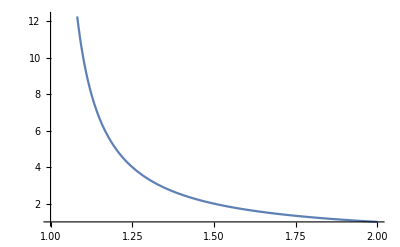

```mathematica
Plot[1/(t-1),{t,1,2}]
```

```mathematica
(2 (a-2 c+a t))/(t^2-1)/.t:>1/(t-1)//Simplify
```

-(2 (-1+t) (-2 c (-1+t)+a t))/((-2+t) t)

```mathematica
(2 (a-2 c+a t))/(t^2-1)
```

```mathematica
((t+1)-(2c)/a)/(t^2-1)-(2c)/a//Factor
```

```mathematica
(ab[1,2,7,8] ab[1,4,5,6])/ab[1,6,7,cap[{8,2},{1,4,5}]]//.capexpand
```

(ab[1,2,7,8] ab[1,4,5,6])/(ab[1,4,5,8] ab[1,6,7,2]+ab[1,6,7,8] ab[2,1,4,5])

```mathematica
ab[1,2,7,8] ab[1,4,5,6]+(ab[1,4,5,8] ab[1,6,7,2]+ab[1,6,7,8] ab[2,1,4,5])//abfactor
```

{ab[1,2,6,8],ab[1,4,5,7]}

```mathematica
-PolyLog[2,z]+PolyLog[2,zb]-1/2 Log[z zb]Log[(1-z)/(1-zb)]-(PolyLog[2,1]-PolyLog[2,z]-PolyLog[2,1-zb]-1/2 Log[z zb]Log[(1-zb)(1-z)]+Log[z]Log[1-zb])//FullSimplify
```

-Log[1-zb] (Log[z]+Log[zb])+1/2 (-Log[(-1+z)/(-1+zb)]+Log[(-1+z) (-1+zb)]) Log[z zb]

```mathematica
-Log[1-zb] (Log[z]+Log[zb])+1/2 (-Log[(-1+z)/(-1+zb)]+Log[(-1+z) (-1+zb)]) Log[z zb]+2 PolyLog[2,z]-2 PolyLog[2,zb]/.{z->1/3,zb->1/7}//FullSimplify
```

0

```mathematica
boxfun1
```

Li[1]-Li[((1+t) (1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])))/(1+t-((-1+t) ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))]-Li[(1+t+((-1+t) ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))/(2+((-1+t) ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8])/(ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))]+log[((1+t) (1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])))/(1+t-((-1+t) ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))] log[(1+t+((-1+t) ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))/(2+((-1+t) ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8])/(ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))]-1/2 log[((1+t) (1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])) (1-(1+t+((-1+t) ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))/(2+((-1+t) ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8])/(ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))))/(1+t-((-1+t) ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))] log[((1-((1+t) (1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])))/(1+t-((-1+t) ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))) (1+t+((-1+t) ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]])))/(2+((-1+t) ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8])/(ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))]

```mathematica
1-(1+t+((-1+t) ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))/(2+((-1+t) ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8])/(ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))
```

-((-1+t) (ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7]-ab[1,2,6,7] ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8]+ab[1,2,6,7] ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))/(ab[1,2,6,7] ((-1+t) ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8]+2 ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))

```mathematica
((1+t) (1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])))/(1+t-((-1+t) ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))
```

((1+t) ab[1,2,6,7] ab[1,4,5,8]-ab[1,2,4,5] ab[1,6,7,8])/((1+t) ab[1,2,6,7] ab[1,4,5,8]+ab[1,2,4,5] ab[1,6,7,8])

```mathematica
(1+t+((-1+t) ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))/(2+((-1+t) ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8])/(ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))/.t->t(1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))^-1//.capexpand/.sortab//Factor//twistorSimplify//twistorSimplify//twistorSimplify//twistorSimplify//twistorSimplify//twistorSimplify
```

-((ab[1,4,5,7] ab[6,7,1,2] (-(1+t) ab[4,5,8,1] ab[6,7,1,2]+ab[1,2,4,5] ab[6,7,8,1]) (-ab[2,6,7,8] ab[4,5,8,1]+ab[2,4,5,8] ab[6,7,8,1])+ab[1,2,4,5] ab[4,5,6,7] ab[6,7,8,1] ((-1+t) ab[4,5,8,1] ab[6,7,1,2]+ab[1,2,4,5] ab[6,7,8,1]) ab[7,8,1,2])/(ab[6,7,1,2] (ab[4,5,8,1] ab[6,7,1,2]-ab[1,2,4,5] ab[6,7,8,1]) (-ab[4,5,8,1] (2 ab[1,4,5,7] ab[2,6,7,8]+(-1+t) ab[4,5,7,8] ab[6,7,1,2])+(2 ab[1,4,5,7] ab[2,4,5,8]-ab[1,2,4,5] ab[4,5,7,8]) ab[6,7,8,1])))

```mathematica
CoefficientList[Denominator[%310/.sortab],t]
```

{2 ab[1,2,6,7] ab[1,4,5,7] ab[1,4,5,8] (-ab[1,2,6,7] ab[1,4,5,8]+ab[1,2,4,5] ab[1,6,7,8]) ab[2,6,7,8]-ab[1,2,6,7]^2 ab[1,4,5,8] (-ab[1,2,6,7] ab[1,4,5,8]+ab[1,2,4,5] ab[1,6,7,8]) ab[4,5,7,8]-ab[1,2,6,7] ab[1,6,7,8] (-ab[1,2,6,7] ab[1,4,5,8]+ab[1,2,4,5] ab[1,6,7,8]) (2 ab[1,4,5,7] ab[2,4,5,8]-ab[1,2,4,5] ab[4,5,7,8]),ab[1,2,6,7]^2 ab[1,4,5,8] (-ab[1,2,6,7] ab[1,4,5,8]+ab[1,2,4,5] ab[1,6,7,8]) ab[4,5,7,8]}

```mathematica
ab[1,2,6,7] ab[1,4,5,8] (-ab[1,2,6,7] ab[1,4,5,8]+ab[1,2,4,5] ab[1,6,7,8]) ab[4,5,7,8]
```

ab[1,2,6,7] ab[1,4,5,8] (ab[1,2,6,7] ab[1,4,5,7] (ab[1,6,7,8] ab[2,4,5,8]-ab[1,4,5,8] ab[2,6,7,8])-ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7])

```mathematica
%310//neab//Simplify
```

(1857764323486417096878534-640635300281076219542441 t)/(624878 (-1802705480688891933+1125996172831997009 t))

```mathematica
2 ab[1,2,6,7] ab[1,4,5,7] ab[1,4,5,8] (-ab[1,2,6,7] ab[1,4,5,8]+ab[1,2,4,5] ab[1,6,7,8]) ab[2,6,7,8]-ab[1,2,6,7]^2 ab[1,4,5,8] (-ab[1,2,6,7] ab[1,4,5,8]+ab[1,2,4,5] ab[1,6,7,8]) ab[4,5,7,8]-ab[1,2,6,7] ab[1,6,7,8] (-ab[1,2,6,7] ab[1,4,5,8]+ab[1,2,4,5] ab[1,6,7,8]) (2 ab[1,4,5,7] ab[2,4,5,8]-ab[1,2,4,5] ab[4,5,7,8])//Simplify
```

ab[1,2,6,7] (ab[1,2,6,7] ab[1,4,5,8]-ab[1,2,4,5] ab[1,6,7,8]) (2 ab[1,4,5,7] (ab[1,6,7,8] ab[2,4,5,8]-ab[1,4,5,8] ab[2,6,7,8])+(ab[1,2,6,7] ab[1,4,5,8]-ab[1,2,4,5] ab[1,6,7,8]) ab[4,5,7,8])

```mathematica
test
```

```mathematica
dlog[(1+t+(2 ab[1,2,7,8] ab[1,4,5,6])/ab[1,6,7,cap[{8,2},{1,4,5}]])/(-1+t+(2 ab[1,2,6,7] ab[1,4,5,6] ab[8,1,2,cap[{5,4},{6,7,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,6,cap[{1,2},{6,7,8}]]))] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,2,4,5,6]+dlog[(a-2 c+a t)^2/(t (a+a t-2 c t))] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,2,4,5,7]-dlog[τ/(2 (a-2 c)+τ)] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,2,4,5,7]+dlog[(1+t-(2 ab[1,2,4,5] ab[1,2,7,8] ab[1,4,6,7])/(ab[1,2,4,7] ab[1,6,7,cap[{8,2},{1,4,5}]]))/(-1+t+(2 ab[1,4,6,7] ab[6,7,8,cap[{5,4},{1,2,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,6,7,8]))] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,2,4,6,7]+dlog[(-1+t+(2 ab[1,5,6,7] ab[8,1,2,cap[{4,5},{6,7,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[5,6,7,8]))/(1+t-(2 ab[1,2,4,5] ab[1,2,7,8] ab[1,5,6,7])/(ab[1,2,5,7] ab[1,6,7,cap[{8,2},{1,4,5}]]))] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,2,5,6,7]+dlog[(1+t)^2/(2 t (a+a t-2 c t))] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,4,5,6,7]+dlog[2 (a-2 c)+τ] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,4,5,6,7]+dlog[(-1+t+(2 ab[1,2,6,7] ab[6,7,8,cap[{5,4},{1,2,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[2,6,7,8]))/(1+t+(2 ab[1,2,4,5] ab[1,2,7,8] ab[4,5,6,7])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[2,4,5,7]))] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[2,4,5,6,7]
```

```mathematica
2 (a-2 c)+τ/.taure//Factor
```

```mathematica
(2 t (a+a t-2 c t))/((-1+t) (1+t))(1+t)^2/(2 t (a+a t-2 c t))
```

(1+t)/(-1+t)

```mathematica
(a-2 c+a t)^2/(t (a+a t-2 c t))/((a-2 c+a t)/(t (a+a t-2 c t)))//Simplify
```

a-2 c+a t

```mathematica
test1=dlog[(1+t+(2 ab[1,2,7,8] ab[1,4,5,6])/ab[1,6,7,cap[{8,2},{1,4,5}]])/(-1+t+(2 ab[1,2,6,7] ab[1,4,5,6] ab[8,1,2,cap[{5,4},{6,7,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,6,cap[{1,2},{6,7,8}]]))] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,2,4,5,6]+dlog[a-2 c+a t] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,2,4,5,7]+dlog[(1+t-(2 ab[1,2,4,5] ab[1,2,7,8] ab[1,4,6,7])/(ab[1,2,4,7] ab[1,6,7,cap[{8,2},{1,4,5}]]))/(-1+t+(2 ab[1,4,6,7] ab[6,7,8,cap[{5,4},{1,2,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,6,7,8]))] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,2,4,6,7]+dlog[(-1+t+(2 ab[1,5,6,7] ab[8,1,2,cap[{4,5},{6,7,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[5,6,7,8]))/(1+t-(2 ab[1,2,4,5] ab[1,2,7,8] ab[1,5,6,7])/(ab[1,2,5,7] ab[1,6,7,cap[{8,2},{1,4,5}]]))] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,2,5,6,7]+dlog[(1+t)/(-1+t)] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,4,5,6,7]+dlog[(-1+t+(2 ab[1,2,6,7] ab[6,7,8,cap[{5,4},{1,2,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[2,6,7,8]))/(1+t+(2 ab[1,2,4,5] ab[1,2,7,8] ab[4,5,6,7])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[2,4,5,7]))] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[2,4,5,6,7];
```

```mathematica
boxfun1
```

Li[1]-Li[((1+t) (1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])))/(1+t-((-1+t) ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))]-Li[(1+t+((-1+t) ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))/(2+((-1+t) ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8])/(ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))]+log[((1+t) (1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])))/(1+t-((-1+t) ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))] log[(1+t+((-1+t) ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))/(2+((-1+t) ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8])/(ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))]-1/2 log[((1+t) (1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])) (1-(1+t+((-1+t) ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))/(2+((-1+t) ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8])/(ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))))/(1+t-((-1+t) ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))] log[((1-((1+t) (1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])))/(1+t-((-1+t) ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))) (1+t+((-1+t) ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]])))/(2+((-1+t) ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8])/(ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))]

```mathematica
1-(1+t+((-1+t) ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))/(2+((-1+t) ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8])/(ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))//Factor//neab//Simplify
```

```mathematica
ac
```

```mathematica
2+((-1+t) ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8])/(ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]])-(1+t+((-1+t) ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))//Simplify//neab
```

(32338653084698027163140073 (-1+t))/18906957723829292388376616

```mathematica
((1+t) (1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])))/(1+t-((-1+t) ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))/.t->(1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))^-1 t//Simplify
```

((1+t) ab[1,2,6,7] ab[1,4,5,8]-ab[1,2,4,5] ab[1,6,7,8])/((1+t) ab[1,2,6,7] ab[1,4,5,8]+ab[1,2,4,5] ab[1,6,7,8])

```mathematica
(ab[1,2,7,8]ab[4,5,6,7])/(ab[1,2,6,7] ab[4,5,7,8])(-1+t)/((-1+t) +(2 ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8]))
```

```mathematica
boxfun11=-Li[((1+t) (1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])))/(1+t-((-1+t) ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))]+Li[(ab[1,2,7,8]ab[4,5,6,7])/(ab[1,2,6,7] ab[4,5,7,8])(-1+t)/((-1+t) +(2 ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8]))]-1/2 log[((1+t) (1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])))/(1+t-((-1+t) ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))(ab[1,2,7,8]ab[4,5,6,7])/(ab[1,2,6,7] ab[4,5,7,8])(-1+t)/((-1+t) +(2 ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8]))]log[(1-((1+t) (1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])))/(1+t-((-1+t) ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])))/(1-(ab[1,2,7,8]ab[4,5,6,7])/(ab[1,2,6,7] ab[4,5,7,8])(-1+t)/((-1+t) +(2 ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8])))];
```

```mathematica
(2 ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8])(1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))//Factor//neab
```

28298717660052214907/451328130452475847629

```mathematica
(2 ab[1,4,5,7]  ab[6,7,8,cap[{1,2},{4,5,8}]])/(ab[1,2,6,7] ab[1,4,5,8]ab[4,5,7,8])+2//Factor
```

(2 (ab[1,2,6,7] ab[1,4,5,8] ab[4,5,7,8]+ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))/(ab[1,2,6,7] ab[1,4,5,8] ab[4,5,7,8])

ab[1,2,6,7] ab[1,4,5,8] ab[4,5,7,8]+ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]

```mathematica
(2 ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8])
```

-(2 ab[1,4,5,7] (-ab[1,2,7,8] ab[4,5,6,7]+ab[1,2,6,7] ab[4,5,7,8]) ab[6,7,8,cap[{1,2},{4,5,8}]])/(ab[1,2,7,8] ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,6,7] ab[4,5,7,8])

```mathematica
(ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7]-ab[1,2,6,7] ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8]+ab[1,2,6,7] ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]])/(-ab[1,2,7,8]ab[4,5,6,7]ab[1,6,7,cap[{8,2},{1,4,5}]])//neab
```

1

```mathematica
boxfun11
```

-Li[((1+t) (1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])))/(1+t-((-1+t) ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))]+Li[((-1+t) ab[1,2,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[4,5,7,8] (-1+t+(2 ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8])))]-1/2 log[((-1+t) (1+t) ab[1,2,7,8] (1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])) ab[4,5,6,7])/(ab[1,2,6,7] (1+t-((-1+t) ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])) ab[4,5,7,8] (-1+t+(2 ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8])))] log[(1-((1+t) (1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])))/(1+t-((-1+t) ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])))/(1-((-1+t) ab[1,2,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[4,5,7,8] (-1+t+(2 ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8]))))]

```mathematica
Limit[((1+t) (1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])))/(1+t-((-1+t) ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])),t->Infinity]
```

1

```mathematica
Limit[((-1+t) ab[1,2,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[4,5,7,8] (-1+t+(2 ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8]))),t->Infinity]
```

(ab[1,2,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[4,5,7,8])

```mathematica
boxfun1
```

```mathematica
-Li[(ab[1,2,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[4,5,7,8])]-1/2 log[((1+t) (1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])) (1-(1+t+((-1+t) ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))/(2+((-1+t) ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8])/(ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))))/(1+t-((-1+t) ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))] log[((1-((1+t) (1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])))/(1+t-((-1+t) ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))) (1+t+((-1+t) ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]])))/(2+((-1+t) ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8])/(ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))]
```

1

```mathematica
Limit[((1+t) (1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])) (1-(1+t+((-1+t) ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))/(2+((-1+t) ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8])/(ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))))/(1+t-((-1+t) ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])),t->Infinity]//Simplify
```

```mathematica
1-(ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7]+ab[1,2,6,7] ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]])/(ab[1,2,6,7] ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8])-(ab[1,2,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[4,5,7,8])//neab
```

0

```mathematica
Limit[((-1+t) ab[1,2,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[4,5,7,8] (-1+t+(2 ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8]))),t->Infinity]
```

(ab[1,2,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[4,5,7,8])

```mathematica
boxfun11[t]
```

(-Li[((1+t) (1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])))/(1+t-((-1+t) ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))]+Li[((-1+t) ab[1,2,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[4,5,7,8] (-1+t+(2 ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8])))]-1/2 log[((-1+t) (1+t) ab[1,2,7,8] (1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])) ab[4,5,6,7])/(ab[1,2,6,7] (1+t-((-1+t) ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])) ab[4,5,7,8] (-1+t+(2 ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8])))] log[(1-((1+t) (1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])))/(1+t-((-1+t) ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])))/(1-((-1+t) ab[1,2,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[4,5,7,8] (-1+t+(2 ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8]))))])[t]

```mathematica
((-1+t) ab[1,2,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[4,5,7,8] (-1+t+(2 ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8])))/.t->(1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))^-1 t
```

```mathematica
(2 ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8])(1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))//neab
```

28298717660052214907/451328130452475847629

```mathematica
(2 (-ab[1,4,5,8]ab[4,5,7,cap[{6,8},{1,2,7}]]-ab[1,2,4,5]ab[1,6,7,8]ab[4,5,7,8]))/(ab[1,2,6,7] ab[1,4,5,8] ab[4,5,7,8])//.capexpand/.sortab//Expand
```

```mathematica
2-(2 ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])-(2 ab[1,2,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[4,5,7,8])+t-((1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])))
```

1+t-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])-(2 ab[1,2,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[4,5,7,8])

```mathematica
test
```

```mathematica
dlog[(1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])+t+(2 ab[1,2,7,8] ab[1,4,5,6])/(ab[1,2,6,7] ab[1,4,5,8]))/(-(1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))+t+(2 ab[1,4,5,6] ab[8,1,2,cap[{5,4},{6,7,8}]])/(ab[1,4,5,8] ab[4,5,6,cap[{1,2},{6,7,8}]]))] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,2,4,5,6]+dlog[(a-2 c+a t)^2/(t (a+a t-2 c t))] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,2,4,5,7]-dlog[τ/(2 (a-2 c)+τ)] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,2,4,5,7]+dlog[(1+t-(2 ab[1,2,4,5] ab[1,2,7,8] ab[1,4,6,7])/(ab[1,2,4,7] ab[1,6,7,cap[{8,2},{1,4,5}]]))/(-1+t+(2 ab[1,4,6,7] ab[6,7,8,cap[{5,4},{1,2,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,6,7,8]))] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,2,4,6,7]+dlog[(-1+t+(2 ab[1,5,6,7] ab[8,1,2,cap[{4,5},{6,7,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[5,6,7,8]))/(1+t-(2 ab[1,2,4,5] ab[1,2,7,8] ab[1,5,6,7])/(ab[1,2,5,7] ab[1,6,7,cap[{8,2},{1,4,5}]]))] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,2,5,6,7]+dlog[(1+t)^2/(2 t (a+a t-2 c t))] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,4,5,6,7]+dlog[2 (a-2 c)+τ] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,4,5,6,7]+dlog[(-1+t+(2 ab[1,2,6,7] ab[6,7,8,cap[{5,4},{1,2,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[2,6,7,8]))/(1+t+(2 ab[1,2,4,5] ab[1,2,7,8] ab[4,5,6,7])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[2,4,5,7]))] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[2,4,5,6,7]
```

```mathematica
1+t+(2 ab[1,2,7,8] ab[1,4,5,6])/ab[1,6,7,cap[{8,2},{1,4,5}]]/.t->(1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))^-1 t
```

```mathematica
1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])+t+(2 ab[1,2,7,8] ab[1,4,5,6])/(ab[1,2,6,7] ab[1,4,5,8])
```

```mathematica
(2 ab[1,2,6,7] ab[1,4,5,6] ab[8,1,2,cap[{5,4},{6,7,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,6,cap[{1,2},{6,7,8}]])(1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))//neab
```

927066871446929059/1162669405371008823

```mathematica
(2 ab[1,2,6,7] ab[1,4,5,6] ab[8,1,2,cap[{5,4},{6,7,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,6,cap[{1,2},{6,7,8}]])(1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))//Factor
```

```mathematica
(2 ab[1,4,5,6] ab[8,1,2,cap[{5,4},{6,7,8}]])/(ab[1,4,5,8] ab[4,5,6,cap[{1,2},{6,7,8}]])//neab
```

927066871446929059/1162669405371008823

```mathematica
taure/.t->(1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))^-1 t//Simplify
```

{τ:>(2 (a-2 c+(a t)/(1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))))/((t/(1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])))^2-1)}

```mathematica
(2 a(1-2 c/a+t/(1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])))(1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))^2)/((t)^2-(1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))^2)
```

-((2 (-ab[1,2,6,7] ab[1,4,5,8]+ab[1,2,4,5] ab[1,6,7,8]) (a ab[1,2,6,7] ab[1,4,5,8]-2 c ab[1,2,6,7] ab[1,4,5,8]+a t ab[1,2,6,7] ab[1,4,5,8]-a ab[1,2,4,5] ab[1,6,7,8]+2 c ab[1,2,4,5] ab[1,6,7,8]))/((ab[1,2,6,7] ab[1,4,5,8]+t ab[1,2,6,7] ab[1,4,5,8]-ab[1,2,4,5] ab[1,6,7,8]) (-ab[1,2,6,7] ab[1,4,5,8]+t ab[1,2,6,7] ab[1,4,5,8]+ab[1,2,4,5] ab[1,6,7,8])))

```mathematica
a/.acre
```

```mathematica
(ab[1,2,3,8] ab[1,2,7,cap[{6,8},{4,5,7}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[2,3,7,8])(1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))//neab
```

-992991459619931148755/1075286589465677022088

```mathematica
(ab[1,2,3,8] ab[1,2,7,cap[{6,8},{4,5,7}]])/(ab[1,2,6,7] ab[1,4,5,8] ab[2,3,7,8])//neab
```

-992991459619931148755/1075286589465677022088

```mathematica
2 c/a/.acre
```

```mathematica
a(1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))/.acre//Factor//neab
```

-992991459619931148755/1075286589465677022088

```mathematica
(2 (ab[1,2,3,8] ab[1,2,7,cap[{6,8},{4,5,7}]])/(ab[1,2,6,7] ab[1,4,5,8] ab[2,3,7,8])(1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])-2 (ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[1,2,7,cap[{6,8},{4,5,7}]] ab[1,4,5,8])+ t))/((t)^2-(1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))^2)
```

-992991459619931148755/1075286589465677022088

```mathematica
(2 ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] (1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])) ab[4,5,6,7])/(ab[1,2,7,cap[{6,8},{4,5,7}]] ab[1,6,7,cap[{8,2},{1,4,5}]])//Factor//neab
```

-19661062931081379474956401/40698618920954757764645262

```mathematica
(2 ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8]  ab[4,5,6,7])/(ab[1,2,6,7]^2  ab[1,4,5,8] ab[4,5,7,8])//neab
```

```mathematica
c/a(1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))/.acre//neab
```

-19661062931081379474956401/81397237841909515529290524

```mathematica
(ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[1,2,7,cap[{6,8},{4,5,7}]] ab[1,4,5,8])//neab
```

-19661062931081379474956401/81397237841909515529290524

```mathematica
Limit[(1-(ab[1,2,4,5] ab[6,7,8,9])/(ab[1,2,6,7] ab[4,5,8,9])-(ab[4,5,6,7] ab[8,9,1,2])/(ab[1,2,6,7] ab[4,5,8,9]))//fullabB,e->0]/.τ->0
```

1-(ab[1,2,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[4,5,7,8])

```mathematica
taure
```

{τ:>(2 (a-2 c+a t))/(t^2-1)}

```mathematica
(t+b-a)/(t^2-b^2)+x//Factor
```

(a-b-t+b^2 x-t^2 x)/((b-t) (b+t))

```mathematica
boxfun1
```

```mathematica
((1+t) (1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])) (((-1+t) ab[1,2,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[4,5,7,8] (-1+t+(2 ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8])))))/(1+t-((-1+t) ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))/.t->τ
```

((-1+τ) (1+τ) ab[1,2,7,8] (1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])) ab[4,5,6,7])/(ab[1,2,6,7] (1+τ-((-1+τ) ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])) ab[4,5,7,8] (-1+τ+(2 ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8])))

```mathematica
logmonic[Factor[((-1+τ) (1+τ) ab[1,2,7,8] (1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])) ab[4,5,6,7])/(ab[1,2,6,7] (1+τ-((-1+τ) ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])) ab[4,5,7,8] (-1+τ+(2 ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8])))]]//Simplify
```

log[(ab[1,2,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[4,5,7,8])]+log[((-1+τ^2) (ab[1,2,6,7] ab[1,4,5,8]-ab[1,2,4,5] ab[1,6,7,8]) ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8])/(((1+τ) ab[1,2,6,7] ab[1,4,5,8]-(-1+τ) ab[1,2,4,5] ab[1,6,7,8]) ((-1+τ) ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8]+2 ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))]

```mathematica
((-1+τ^2) (ab[1,2,6,7] ab[1,4,5,8]-ab[1,2,4,5] ab[1,6,7,8]) ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8])/(((1+τ) ab[1,2,6,7] ab[1,4,5,8]-(-1+τ) ab[1,2,4,5] ab[1,6,7,8]) ((-1+τ) ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8]+2 ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))//neab//Simplify
```

(5721111791458130223658960027276693 (-1+τ^2))/((-1049749640281961+102501433217393 τ) (-71985640161930362905+55814944356186240101 τ))

```mathematica
((ab[1,2,6,7] ab[1,4,5,8]-ab[1,2,4,5] ab[1,6,7,8]) ab[1,6,7,cap[{8,2},{1,4,5}]]ab[4,5,7,8])/5721111791458130223658960027276693//neab
```

```mathematica
567//PrimeQ
```

False

```mathematica
logmonic[Factor[((1+τ) ab[1,2,6,7] ab[1,4,5,8]-ab[1,2,4,5] ab[1,6,7,8])/((1+τ) ab[1,2,6,7] ab[1,4,5,8]+ab[1,2,4,5] ab[1,6,7,8])]]//Simplify
```

log[1]+log[((1+τ) ab[1,2,6,7] ab[1,4,5,8]-ab[1,2,4,5] ab[1,6,7,8])/((1+τ) ab[1,2,6,7] ab[1,4,5,8]+ab[1,2,4,5] ab[1,6,7,8])]

```mathematica
((1+τ) (1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])))/(1+τ-((-1+τ) ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))/.τ->(1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))^-1 τ//Simplify
```

```mathematica
Last[DeleteCases[CoefficientList[Numerator[(1+τ) ab[1,2,6,7] ab[1,4,5,8]+ab[1,2,4,5] ab[1,6,7,8]],τ],0]]
```

ab[1,2,6,7] ab[1,4,5,8]

```mathematica
logmonic[Factor[1-(ab[1,2,7,8] (-(1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))+τ) ab[4,5,6,7])/(ab[1,2,6,7] ab[4,5,7,8] (1+τ-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])-(2 ab[1,2,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[4,5,7,8])))]]
```

log[(-ab[1,2,6,7] ab[1,2,7,8] ab[1,4,5,8] ab[4,5,6,7]+ab[1,2,6,7]^2 ab[1,4,5,8] ab[4,5,7,8])/(ab[1,2,6,7]^2 ab[1,4,5,8] ab[4,5,7,8])]+log[1/(1+τ-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])-(2 ab[1,2,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[4,5,7,8]))(-(ab[1,2,6,7] ab[1,2,7,8] ab[1,4,5,8] ab[4,5,6,7])/(-ab[1,2,6,7] ab[1,2,7,8] ab[1,4,5,8] ab[4,5,6,7]+ab[1,2,6,7]^2 ab[1,4,5,8] ab[4,5,7,8])-(τ ab[1,2,6,7] ab[1,2,7,8] ab[1,4,5,8] ab[4,5,6,7])/(-ab[1,2,6,7] ab[1,2,7,8] ab[1,4,5,8] ab[4,5,6,7]+ab[1,2,6,7]^2 ab[1,4,5,8] ab[4,5,7,8])-(ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7])/(-ab[1,2,6,7] ab[1,2,7,8] ab[1,4,5,8] ab[4,5,6,7]+ab[1,2,6,7]^2 ab[1,4,5,8] ab[4,5,7,8])+(ab[1,2,6,7]^2 ab[1,4,5,8] ab[4,5,7,8])/(-ab[1,2,6,7] ab[1,2,7,8] ab[1,4,5,8] ab[4,5,6,7]+ab[1,2,6,7]^2 ab[1,4,5,8] ab[4,5,7,8])+(τ ab[1,2,6,7]^2 ab[1,4,5,8] ab[4,5,7,8])/(-ab[1,2,6,7] ab[1,2,7,8] ab[1,4,5,8] ab[4,5,6,7]+ab[1,2,6,7]^2 ab[1,4,5,8] ab[4,5,7,8])-(ab[1,2,4,5] ab[1,2,6,7] ab[1,6,7,8] ab[4,5,7,8])/(-ab[1,2,6,7] ab[1,2,7,8] ab[1,4,5,8] ab[4,5,6,7]+ab[1,2,6,7]^2 ab[1,4,5,8] ab[4,5,7,8]))]

```mathematica
1-(ab[1,2,7,8] (-(1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))+τ) ab[4,5,6,7])/(ab[1,2,6,7] ab[4,5,7,8] (1+τ-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])-(2 ab[1,2,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[4,5,7,8])))//neabp//Simplify
```

```mathematica
Limit[(40 (8304102025265+10904495035837 τ))/(208403 (-248257967+4099078607 τ)),τ->Infinity]
```

1383320/2709239

```mathematica
test
```

dlog[(1+t+(2 ab[1,2,7,8] ab[1,4,5,6])/ab[1,6,7,cap[{8,2},{1,4,5}]])/(-1+t+(2 ab[1,2,6,7] ab[1,4,5,6] ab[8,1,2,cap[{5,4},{6,7,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,6,cap[{1,2},{6,7,8}]]))] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,2,4,5,6]+dlog[(a-2 c+a t)^2/(a t (a+a t-2 c t))] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,2,4,5,7]-dlog[τ/(2 (a-2 c)+τ)] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,2,4,5,7]+dlog[(1+t-(2 ab[1,2,4,5] ab[1,2,7,8] ab[1,4,6,7])/(ab[1,2,4,7] ab[1,6,7,cap[{8,2},{1,4,5}]]))/(-1+t+(2 ab[1,4,6,7] ab[6,7,8,cap[{5,4},{1,2,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,6,7,8]))] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,2,4,6,7]+dlog[(-1+t+(2 ab[1,5,6,7] ab[8,1,2,cap[{4,5},{6,7,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[5,6,7,8]))/(1+t-(2 ab[1,2,4,5] ab[1,2,7,8] ab[1,5,6,7])/(ab[1,2,5,7] ab[1,6,7,cap[{8,2},{1,4,5}]]))] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,2,5,6,7]+dlog[(1+t)^2/(2 t (a+a t-2 c t))] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,4,5,6,7]+dlog[2 (a-2 c)+τ] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,4,5,6,7]+dlog[(-1+t+(2 ab[1,2,6,7] ab[6,7,8,cap[{5,4},{1,2,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[2,6,7,8]))/(1+t+(2 ab[1,2,4,5] ab[1,2,7,8] ab[4,5,6,7])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[2,4,5,7]))] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[2,4,5,6,7]

```mathematica
boxfun1
```

```mathematica
Li[1]-Li[((1+t) (1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])))/(1+t-((-1+t) ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))]-Li[(1+t+((-1+t) ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))/(2+((-1+t) ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8])/(ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))]+log[((1+t) (1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])))/(1+t-((-1+t) ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))] log[(1+t+((-1+t) ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))/(2+((-1+t) ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8])/(ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))]-1/2 log[1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])] log[((ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]) (1+t+((-1+t) ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]])))/(2+((-1+t) ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8])/(ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))]
```

```mathematica
τ/.taure
```

(2 (a-2 c+a t))/(-1+t^2)

```mathematica
(1+t+((-1+t) ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))/(2+((-1+t) ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8])/(ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))/.t->1
```

1

```mathematica
((1+t) (1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])))/(1+t-((-1+t) ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))/.t->1
```

1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])

```mathematica
boxfun1
```

Li[1]-Li[((1+t) (1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])))/(1+t-((-1+t) ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))]-Li[(1+t+((-1+t) ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))/(2+((-1+t) ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8])/(ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))]+log[((1+t) (1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])))/(1+t-((-1+t) ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))] log[(1+t+((-1+t) ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))/(2+((-1+t) ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8])/(ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))]-1/2 log[((1+t) (1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])) (1-(1+t+((-1+t) ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))/(2+((-1+t) ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8])/(ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))))/(1+t-((-1+t) ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))] log[((1-((1+t) (1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])))/(1+t-((-1+t) ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))) (1+t+((-1+t) ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]])))/(2+((-1+t) ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8])/(ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))]

```mathematica
(Limit[((2 (a-2 c+a t))/(-1+t^2))(1-(1+t+((-1+t) ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))/(2+((-1+t) ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8])/(ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))),t->1]//Simplify)/.acre/.capexpand//Simplify//twistorSimplify//twistorSimplify//twistorSimplify//twistorSimplify//twistorSimplify
```

```mathematica
(ab[2,3,8,1] (ab[4,5,7,8] (-ab[4,5,8,1] ab[6,7,1,2]+ab[1,2,4,5] ab[6,7,8,1])+ab[4,5,6,7] ab[4,5,8,1] ab[7,8,1,2]) (ab[4,5,8,1] ab[6,7,1,2] (ab[1,4,5,7] ab[2,6,7,8]-ab[4,5,7,8] ab[6,7,1,2]+ab[2,4,5,7] ab[6,7,8,1])+ab[1,2,4,5] ab[4,5,6,7] ab[6,7,8,1] ab[7,8,1,2]))/(ab[1,4,5,7] (ab[4,5,8,1] ab[6,7,1,2]-ab[1,2,4,5] ab[6,7,8,1])^2 (ab[2,6,7,8] ab[4,5,8,1]-ab[2,4,5,8] ab[6,7,8,1]) ab[7,8,2,3])/.sortab
```

```mathematica
-((ab[1,2,3,8] (-ab[1,2,7,8] ab[1,4,5,8] ab[4,5,6,7]+(ab[1,2,6,7] ab[1,4,5,8]-ab[1,2,4,5] ab[1,6,7,8]) ab[4,5,7,8]) (-ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7]-ab[1,2,6,7] ab[1,4,5,8] (-ab[1,6,7,8] ab[2,4,5,7]+ab[1,4,5,7] ab[2,6,7,8]-ab[1,2,6,7] ab[4,5,7,8])))/(ab[1,4,5,7] (-ab[1,2,6,7] ab[1,4,5,8]+ab[1,2,4,5] ab[1,6,7,8])^2 ab[2,3,7,8] (ab[1,6,7,8] ab[2,4,5,8]-ab[1,4,5,8] ab[2,6,7,8])))//Simplify
```

```mathematica
-((ab[1,2,3,8] (-ab[1,4,5,7](ab[1,6,7,8] ab[2,4,5,8]-ab[1,4,5,8] ab[2,6,7,8])) (-ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7]+ab[1,2,6,7] ab[1,4,5,8] (ab[1,6,7,8] ab[2,4,5,7]-ab[1,4,5,7] ab[2,6,7,8]+ab[1,2,6,7] ab[4,5,7,8])))/(ab[1,4,5,7] (ab[1,2,6,7] ab[1,4,5,8]-ab[1,2,4,5] ab[1,6,7,8])^2 ab[2,3,7,8] (ab[1,6,7,8] ab[2,4,5,8]-ab[1,4,5,8] ab[2,6,7,8])))//Simplify
```

```mathematica
(ab[1,2,3,8] (ab[1,2,7,8]ab[4,5,6,7](ab[1,2,6,7] ab[1,4,5,8]-ab[1,2,4,5] ab[1,6,7,8])))/((ab[1,2,6,7] ab[1,4,5,8]-ab[1,2,4,5] ab[1,6,7,8])^2 ab[2,3,7,8])
```

(ab[1,2,3,8] ab[1,2,7,8] ab[4,5,6,7])/((ab[1,2,6,7] ab[1,4,5,8]-ab[1,2,4,5] ab[1,6,7,8]) ab[2,3,7,8])

```mathematica
(-ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7]+ab[1,2,6,7] ab[1,4,5,8] (ab[1,6,7,8] ab[2,4,5,7]-ab[1,4,5,7] ab[2,6,7,8]+ab[1,2,6,7] ab[4,5,7,8]))/(ab[1,2,7,8]ab[4,5,6,7](ab[1,2,6,7] ab[1,4,5,8]-ab[1,2,4,5] ab[1,6,7,8]))//neab
```

1

```mathematica
boxfun11
```

-Li[((1+t) (1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])))/(1+t-((-1+t) ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))]+Li[((-1+t) ab[1,2,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[4,5,7,8] (-1+t+(2 ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8])))]-1/2 log[((-1+t) (1+t) ab[1,2,7,8] (1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])) ab[4,5,6,7])/(ab[1,2,6,7] (1+t-((-1+t) ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])) ab[4,5,7,8] (-1+t+(2 ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8])))] log[(1-((1+t) (1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])))/(1+t-((-1+t) ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])))/(1-((-1+t) ab[1,2,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[4,5,7,8] (-1+t+(2 ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8]))))]

```mathematica
Limit[((1+t) (1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])))/(1+t-((-1+t) ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])),t->Infinity]
```

1

```mathematica
Limit[((1-((1+t) (1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])))/(1+t-((-1+t) ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])))t)/(1-((-1+t) ab[1,2,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[4,5,7,8] (-1+t+(2 ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8])))),t->Infinity]//Simplify
```

(2 ab[1,2,4,5] ab[1,2,6,7] ab[1,6,7,8] ab[4,5,7,8])/((ab[1,2,6,7] ab[1,4,5,8]-ab[1,2,4,5] ab[1,6,7,8]) (-ab[1,2,7,8] ab[4,5,6,7]+ab[1,2,6,7] ab[4,5,7,8]))

```mathematica
taure/.t->(1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))^-1 t
```

{τ:>(2 (a-2 c+(a t)/(1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))))/((t/(1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])))^2-1)}

```mathematica
(2 (ab[1,2,3,8] ab[1,2,7,cap[{6,8},{4,5,7}]])/(ab[1,2,6,7] ab[1,4,5,8]  ab[2,3,7,8])((1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))-2 (ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8]  ab[4,5,6,7])/(ab[1,2,6,7] ab[1,2,7,cap[{6,8},{4,5,7}]] ab[1,4,5,8])+ t))/((t)-(1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))^2)
```

-8422660205080914720/755852824730165059897

```mathematica
(1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))c/a/.acre//Factor//neab
```

4918711204615996057066380171/1236405395341096264125082988

```mathematica
(ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8]  ab[4,5,6,7])/(ab[1,2,6,7] ab[1,2,7,cap[{6,8},{4,5,7}]] ab[1,4,5,8])//neab
```

-4918711204615996057066380171/1236405395341096264125082988

```mathematica
boxfun1
```

```mathematica
Li[1]-Li[((1+t) (1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])))/(1+t-((-1+t) ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))]-Li[1-(ab[1,2,7,8]ab[4,5,6,7])/(ab[1,2,6,7]ab[4,5,7,8])(-1+t)/((-1+t)  +2 (ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]])/(ab[4,5,7,8]ab[1,6,7,cap[{8,2},{1,4,5}]]))]+log[((1+t) (1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])))/(1+t-((-1+t) ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))] log[(1+t+((-1+t) ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))/(2+((-1+t) ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8])/(ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))]-1/2 log[((1+t) (1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])) (1-(1+t+((-1+t) ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))/(2+((-1+t) ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8])/(ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))))/(1+t-((-1+t) ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))] log[((1-((1+t) (1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])))/(1+t-((-1+t) ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))) (1+t+((-1+t) ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]])))/(2+((-1+t) ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8])/(ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))]
```

```mathematica
((1+t+((-1+t) ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))/(2+((-1+t) ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8])/(ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]])))/(1-(ab[1,2,7,8]ab[4,5,6,7])/(ab[1,2,6,7]ab[4,5,7,8])(-1+t)/((-1+t)  +2 (ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]])/(ab[4,5,7,8]ab[1,6,7,cap[{8,2},{1,4,5}]])))//neab//Simplify
```

1

```mathematica
Limit[(1+t+((-1+t) ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))/(2+((-1+t) ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8])/(ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]])),t->Infinity]//Simplify
```

```mathematica
(ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7]+ab[1,2,6,7] ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]])/(ab[1,2,6,7] ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8])//neab
```

-16296455779508/91981339247005

```mathematica
Limit[1-(ab[1,2,7,8]ab[4,5,6,7])/(ab[1,2,6,7]ab[4,5,7,8])(-1+t)/((-1+t)  +2 (ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]])/(ab[4,5,7,8]ab[1,6,7,cap[{8,2},{1,4,5}]])),t->Infinity]//Simplify
```

```mathematica
1-(ab[1,2,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[4,5,7,8])//neab
```

-16296455779508/91981339247005

```mathematica
1+t-((-1+t) ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])-(1+t) (1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))//Simplify
```

(2 ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])

```mathematica
test1
```

dlog[(-1+t+(2 ab[1,2,6,8] ab[1,4,5,7])/ab[1,6,7,cap[{4,5},{1,2,8}]])/(-1+t+(2 ab[1,2,6,7] ab[1,4,5,6] ab[8,1,2,cap[{5,4},{6,7,8}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,6,cap[{1,2},{6,7,8}]]))] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,2,4,5,6]+dlog[-1+t+(2 ab[1,2,6,7] ab[1,4,5,7] ab[cap[{4,5},{1,2,8}],6,7,8])/(ab[1,2,7,cap[{4,5},{6,7,8}]] ab[1,6,7,cap[{4,5},{1,2,8}]])] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,2,4,5,7]+dlog[(-1+t+(2 ab[1,2,4,8] ab[1,2,6,7] ab[1,4,5,7])/(ab[1,2,4,7] ab[1,6,7,cap[{4,5},{1,2,8}]]))/(-1+t+(2 ab[1,4,6,7] ab[cap[{4,5},{1,2,8}],6,7,8])/(ab[1,6,7,cap[{4,5},{1,2,8}]] ab[4,6,7,8]))] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,2,4,6,7]+dlog[(-1+t+(2 ab[1,5,6,7] ab[cap[{4,5},{1,2,8}],6,7,8])/(ab[1,6,7,cap[{4,5},{1,2,8}]] ab[5,6,7,8]))/(-1+t+(2 ab[1,2,5,8] ab[1,2,6,7] ab[1,4,5,7])/(ab[1,2,5,7] ab[1,6,7,cap[{4,5},{1,2,8}]]))] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,2,5,6,7]+dlog[(1+t)/(-1+t)] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,4,5,6,7]+dlog[(-1+t+(2 ab[1,2,6,7] ab[cap[{4,5},{1,2,8}],6,7,8])/(ab[1,6,7,cap[{4,5},{1,2,8}]] ab[2,6,7,8]))/(-1+t+(2 ab[1,4,5,7] ab[2,6,7,cap[{4,5},{1,2,8}]])/(ab[1,6,7,cap[{4,5},{1,2,8}]] ab[2,4,5,7]))] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[2,4,5,6,7]

```mathematica
int1[dlog[(1+t)/(-1+t)]boxfun1-(dlog[τ+1](-Li[1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])]-1/2 log[(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])] (log[(ab[1,2,3,8] ab[1,2,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[1,4,5,8] ab[2,3,7,8])]-log[τ])))/.taure/.acre/.{dlog[x_]:>D[Log[x],t],log:>Log,Li[x_]:>PolyLog[2,x]}]
```

int1[-((((2 ab[1,2,3,8] ab[1,2,7,cap[{6,8},{4,5,7}]])/((-1+t^2) ab[1,6,7,cap[{8,2},{1,4,5}]] ab[2,3,7,8])-(4 t ((ab[1,2,3,8] ab[1,2,7,cap[{6,8},{4,5,7}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[2,3,7,8])+(t ab[1,2,3,8] ab[1,2,7,cap[{6,8},{4,5,7}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[2,3,7,8])-(2 ab[1,2,3,8] ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7])/(ab[1,6,7,cap[{8,2},{1,4,5}]]^2 ab[2,3,7,8])))/((-1+t^2)^2)) (-1/2 Log[(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])] (Log[(ab[1,2,3,8] ab[1,2,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[1,4,5,8] ab[2,3,7,8])]-Log[(2 ((ab[1,2,3,8] ab[1,2,7,cap[{6,8},{4,5,7}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[2,3,7,8])+(t ab[1,2,3,8] ab[1,2,7,cap[{6,8},{4,5,7}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[2,3,7,8])-(2 ab[1,2,3,8] ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7])/(ab[1,6,7,cap[{8,2},{1,4,5}]]^2 ab[2,3,7,8])))/(-1+t^2)])-PolyLog[2,1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])]))/(1+(2 ((ab[1,2,3,8] ab[1,2,7,cap[{6,8},{4,5,7}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[2,3,7,8])+(t ab[1,2,3,8] ab[1,2,7,cap[{6,8},{4,5,7}]])/(ab[1,6,7,cap[{8,2},{1,4,5}]] ab[2,3,7,8])-(2 ab[1,2,3,8] ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7])/(ab[1,6,7,cap[{8,2},{1,4,5}]]^2 ab[2,3,7,8])))/(-1+t^2)))+1/(1+t)(-1+t) (1/(-1+t)-(1+t)/(-1+t)^2) (π^2/6+Log[((1+t) (1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])))/(1+t-((-1+t) ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))] Log[(1+t+((-1+t) ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))/(2+((-1+t) ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8])/(ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))]-1/2 Log[((1+t) (1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])) (1-(1+t+((-1+t) ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))/(2+((-1+t) ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8])/(ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))))/(1+t-((-1+t) ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))] Log[((1-((1+t) (1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])))/(1+t-((-1+t) ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))) (1+t+((-1+t) ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]])))/(2+((-1+t) ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8])/(ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))]-PolyLog[2,((1+t) (1-(ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8])))/(1+t-((-1+t) ab[1,2,4,5] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,4,5,8]))]-PolyLog[2,(1+t+((-1+t) ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7])/(ab[1,2,6,7] ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))/(2+((-1+t) ab[1,6,7,cap[{8,2},{1,4,5}]] ab[4,5,7,8])/(ab[1,4,5,7] ab[6,7,8,cap[{1,2},{4,5,8}]]))])]

```mathematica
NIntegrate[%460,{t,1,Infinity}]
```

33.1867

```mathematica
dlog[-1+t+(2 ab[1,2,6,7] ab[1,4,5,7] ab[cap[{4,5},{1,2,8}],6,7,8])/(ab[1,2,7,cap[{4,5},{6,7,8}]] ab[1,6,7,cap[{4,5},{1,2,8}]])] Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,2,4,5,7]
```

```mathematica
Qlog[ab[7,8,1,2]/ab[7,8,1,6]] R[1,2,4,5,7]dlog[τ/(τ+1)],-Li[1-(ab[1,2,7,8]ab[4,5,6,7])/(ab[1,2,6,7]ab[4,5,7,8])]-1/2(log[τ]+log[(ab[1,2,4,5]ab[1,6,7,8]ab[2,3,7,8])/(ab[1,2,3,8]ab[1,2,6,7]ab[4,5,7,8])])log[(ab[1,2,7,8]ab[4,5,6,7])/(ab[1,2,6,7]ab[4,5,7,8])]
```

```mathematica
dlog[-1+t+(2 ab[1,2,6,7] ab[1,4,5,7] ab[cap[{4,5},{1,2,8}],6,7,8])/(ab[1,2,7,cap[{4,5},{6,7,8}]] ab[1,6,7,cap[{4,5},{1,2,8}]])] boxfun1+dlog[τ/(τ+1)](-Li[1-(ab[1,2,7,8]ab[4,5,6,7])/(ab[1,2,6,7]ab[4,5,7,8])]-1/2(log[τ]+log[(ab[1,2,4,5]ab[1,6,7,8]ab[2,3,7,8])/(ab[1,2,3,8]ab[1,2,6,7]ab[4,5,7,8])])log[(ab[1,2,7,8]ab[4,5,6,7])/(ab[1,2,6,7]ab[4,5,7,8])])/.taure/.acre/.{dlog[x_]:>D[Log[x],t],log:>Log,Li[x_]:>PolyLog[2,x]};
```

2.16362

```mathematica
boxfun2=boxfun1/.{4->3,5->4}
```

Li[1]-Li[((1+t) (1-(ab[1,2,3,4] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,3,4,8])))/(1+t-((-1+t) ab[1,2,3,4] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,3,4,8]))]-Li[(1+t+((-1+t) ab[1,2,3,4] ab[1,2,7,8] ab[1,6,7,8] ab[3,4,6,7])/(ab[1,2,6,7] ab[1,3,4,7] ab[6,7,8,cap[{1,2},{3,4,8}]]))/(2+((-1+t) ab[1,6,7,cap[{8,2},{1,3,4}]] ab[3,4,7,8])/(ab[1,3,4,7] ab[6,7,8,cap[{1,2},{3,4,8}]]))]+log[((1+t) (1-(ab[1,2,3,4] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,3,4,8])))/(1+t-((-1+t) ab[1,2,3,4] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,3,4,8]))] log[(1+t+((-1+t) ab[1,2,3,4] ab[1,2,7,8] ab[1,6,7,8] ab[3,4,6,7])/(ab[1,2,6,7] ab[1,3,4,7] ab[6,7,8,cap[{1,2},{3,4,8}]]))/(2+((-1+t) ab[1,6,7,cap[{8,2},{1,3,4}]] ab[3,4,7,8])/(ab[1,3,4,7] ab[6,7,8,cap[{1,2},{3,4,8}]]))]-1/2 log[((1+t) (1-(ab[1,2,3,4] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,3,4,8])) (1-(1+t+((-1+t) ab[1,2,3,4] ab[1,2,7,8] ab[1,6,7,8] ab[3,4,6,7])/(ab[1,2,6,7] ab[1,3,4,7] ab[6,7,8,cap[{1,2},{3,4,8}]]))/(2+((-1+t) ab[1,6,7,cap[{8,2},{1,3,4}]] ab[3,4,7,8])/(ab[1,3,4,7] ab[6,7,8,cap[{1,2},{3,4,8}]]))))/(1+t-((-1+t) ab[1,2,3,4] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,3,4,8]))] log[((1-((1+t) (1-(ab[1,2,3,4] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,3,4,8])))/(1+t-((-1+t) ab[1,2,3,4] ab[1,6,7,8])/(ab[1,2,6,7] ab[1,3,4,8]))) (1+t+((-1+t) ab[1,2,3,4] ab[1,2,7,8] ab[1,6,7,8] ab[3,4,6,7])/(ab[1,2,6,7] ab[1,3,4,7] ab[6,7,8,cap[{1,2},{3,4,8}]])))/(2+((-1+t) ab[1,6,7,cap[{8,2},{1,3,4}]] ab[3,4,7,8])/(ab[1,3,4,7] ab[6,7,8,cap[{1,2},{3,4,8}]]))]

```mathematica
dlog[-1+t+(2 ab[1,2,6,7] ab[1,3,4,7] ab[cap[{3,4},{1,2,8}],6,7,8])/(ab[1,2,7,cap[{3,4},{6,7,8}]] ab[1,6,7,cap[{3,4},{1,2,8}]])] boxfun2-dlog[τ/(τ+1)](-Li[1-(ab[1,2,7,8]ab[3,4,6,7])/(ab[1,2,6,7]ab[3,4,7,8])]-1/2(log[τ]+log[(ab[1,2,3,4]ab[1,6,7,8]ab[2,3,7,8])/(ab[1,2,3,8]ab[1,2,6,7]ab[3,4,7,8])])log[(ab[1,2,7,8]ab[3,4,6,7])/(ab[1,2,6,7]ab[3,4,7,8])])/.taure1/.{dlog[x_]:>D[Log[x,t]],log:>Log,Li[x_]:>PolyLog[2,x]}//neabp
```

-(Log[t] (1/2 Log[10795350/6954671] (-Log[47652474125/7330964928]+Log[(2 (19213131237997633086325/758344387732408847071032+(3560213416025 t)/134705844378264))/(-1+t^2)])-PolyLog[2,3840679/10795350]))/Log[(2 (19213131237997633086325/758344387732408847071032+(3560213416025 t)/134705844378264))/((-1+t^2) (1+(2 (19213131237997633086325/758344387732408847071032+(3560213416025 t)/134705844378264))/(-1+t^2)))]+1/Log[20726698387764107/21621610986328427+t]Log[t] (π^2/6+Log[(5629632413 (1+t))/(5693971373 (1-(64338960 (-1+t))/5693971373+t))] Log[(1+(447456299282160 (-1+t))/21174154687046267+t)/(2+(844444861950 (-1+t))/294212156443)]-1/2 Log[((1+(447456299282160 (-1+t))/21174154687046267+t) (1-(5629632413 (1+t))/(5693971373 (1-(64338960 (-1+t))/5693971373+t))))/(2+(844444861950 (-1+t))/294212156443)] Log[(5629632413 (1+t) (1-(1+(447456299282160 (-1+t))/21174154687046267+t)/(2+(844444861950 (-1+t))/294212156443)))/(5693971373 (1-(64338960 (-1+t))/5693971373+t))]-PolyLog[2,(5629632413 (1+t))/(5693971373 (1-(64338960 (-1+t))/5693971373+t))]-PolyLog[2,(1+(447456299282160 (-1+t))/21174154687046267+t)/(2+(844444861950 (-1+t))/294212156443)])

(2 ((ab[1,2,3,8] ab[1,2,7,cap[{6,8},{3,4,7}]])/(ab[1,6,7,cap[{8,2},{1,3,4}]] ab[2,3,7,8])+(t ab[1,2,3,8] ab[1,2,7,cap[{6,8},{3,4,7}]])/(ab[1,6,7,cap[{8,2},{1,3,4}]] ab[2,3,7,8])-(2 ab[1,2,3,4] ab[1,2,3,8] ab[1,2,7,8] ab[1,6,7,8] ab[3,4,6,7])/(ab[1,6,7,cap[{8,2},{1,3,4}]]^2 ab[2,3,7,8])))/((-1+t^2) (1+(2 ((ab[1,2,3,8] ab[1,2,7,cap[{6,8},{3,4,7}]])/(ab[1,6,7,cap[{8,2},{1,3,4}]] ab[2,3,7,8])+(t ab[1,2,3,8] ab[1,2,7,cap[{6,8},{3,4,7}]])/(ab[1,6,7,cap[{8,2},{1,3,4}]] ab[2,3,7,8])-(2 ab[1,2,3,4] ab[1,2,3,8] ab[1,2,7,8] ab[1,6,7,8] ab[3,4,6,7])/(ab[1,6,7,cap[{8,2},{1,3,4}]]^2 ab[2,3,7,8])))/(-1+t^2)))

```mathematica
taure1=taure/.acre/.{5->4,4->3}
```

{τ:>(2 ((ab[1,2,3,8] ab[1,2,7,cap[{6,8},{3,4,7}]])/(ab[2,3,7,8] ab[1,6,7,cap[{8,2},{1,3,4}]])-(2 (ab[1,2,3,8] ab[1,2,3,4] ab[1,2,7,8] ab[1,6,7,8] ab[3,4,6,7]))/(ab[2,3,7,8] ab[1,6,7,cap[{8,2},{1,3,4}]]^2)+((ab[1,2,3,8] ab[1,2,7,cap[{6,8},{3,4,7}]]) t)/(ab[2,3,7,8] ab[1,6,7,cap[{8,2},{1,3,4}]])))/(t^2-1)}

```mathematica
Limit[%495,t->Infinity]
```

-∞

```mathematica
(%463//.capexpand)/.ab[z___,4,y___]:>ab[z,3,y]/.ab[z___,5,y___]:>ab[z,4,y]
```

int1[-((-(4 (19213131237997633086325/758344387732408847071032+(3560213416025 t)/134705844378264) t)/((-1+t^2)^2)+3560213416025/(67352922189132 (-1+t^2))) (1/2 Log[5693971373/64338960] (-Log[2233530278904/105685346725]-Log[(2 (19213131237997633086325/758344387732408847071032+(3560213416025 t)/134705844378264))/(-1+t^2)])-PolyLog[2,5629632413/5693971373]))/(1+(2 (19213131237997633086325/758344387732408847071032+(3560213416025 t)/134705844378264))/(-1+t^2))+1/(1+t)(-1+t) (1/(-1+t)-(1+t)/(-1+t)^2) (π^2/6+Log[(5629632413 (1+t))/(5693971373 (1-(64338960 (-1+t))/5693971373+t))] Log[(1+(447456299282160 (-1+t))/21174154687046267+t)/(2+(844444861950 (-1+t))/294212156443)]-1/2 Log[((1+(447456299282160 (-1+t))/21174154687046267+t) (1-(5629632413 (1+t))/(5693971373 (1-(64338960 (-1+t))/5693971373+t))))/(2+(844444861950 (-1+t))/294212156443)] Log[(5629632413 (1+t) (1-(1+(447456299282160 (-1+t))/21174154687046267+t)/(2+(844444861950 (-1+t))/294212156443)))/(5693971373 (1-(64338960 (-1+t))/5693971373+t))]-PolyLog[2,(5629632413 (1+t))/(5693971373 (1-(64338960 (-1+t))/5693971373+t))]-PolyLog[2,(1+(447456299282160 (-1+t))/21174154687046267+t)/(2+(844444861950 (-1+t))/294212156443)])]

```mathematica
%502/.int1[x_]:>NIntegrate[x//Simplify,{t,1,Infinity}]
```

21.3483

```mathematica
τ/.taure/.t->2t+1//Simplify
```

(a-c+a t)/(t+t^2)

```mathematica
1-c/a/.acre
```

```mathematica
1-(ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7])/(ab[1,2,7,cap[{6,8},{4,5,7}]] ab[1,6,7,cap[{8,2},{1,4,5}]])//Factor//neabp
```

67536632263529/68880066745385

```mathematica
(ab[1,2,6,7]ab[1,4,5,7]ab[8,cap1[{1,2},{4,5},{6,7}]])/(ab[7,cap1[{1,2},{4,5},{8,6}]]ab[1,cap1[{4,5},{6,7},{8,2}]])//neabp
```

67536632263529/68880066745385

```mathematica
(ab[1,2,6,7]ab[1,4,5,7]ab[cap[{4,5},{1,2,8}],6,7,8])/(ab[1,2,7,cap[{4,5},{6,7,8}]] ab[1,6,7,cap[{4,5},{1,2,8}]])//neabp
```

67536632263529/68880066745385

-1214400075/8192

```mathematica
(-ab[1,2,7,cap[{6,8},{4,5,7}]] ab[1,6,7,cap[{8,2},{1,4,5}]]+ab[1,2,4,5] ab[1,2,7,8] ab[1,6,7,8] ab[4,5,6,7])/(ab[1,2,6,7]ab[1,4,5,7]ab[8,cap1[{1,2},{4,5},{6,7}]])//neabp
```

-1